## 2D Depth-Projected Shallow Flow (with vertical transport, periodic in x)

## Function Definitions

### Tools

```mathematica
Clear["Global`*"]

interpolate[pts_,val_,dim_]:=Block[{len=Length[Flatten[val]]},
Interpolation[ArrayReshape[Flatten[Thread[{ArrayReshape[Flatten[pts],{len,dim}],Flatten[val]}]],{len,dim+1}],InterpolationOrder->1]
]
iSize=400;
color={Red,Green,Blue,Purple};
```

### Matrix Assemblation for 2D Data

```mathematica
Clear[H,dt,nx,ny,LS,A,id,R,χ]

Assemble[dt_,H_]:=Block[{nx,ny,id},
{nx,ny}=Dimensions[H];

A=SparseArray`SparseBlockMatrix[
Table[{ix,ix}->SparseArray[{
{1,1}->-R/(H⟦ix,1⟧^2 dy^2)(4 (3 H⟦ix,1⟧dy+2 χ))/(3 H⟦ix,1⟧dy+8 χ),{1,2}->-R/(H⟦ix,1⟧^2 dy^2)(4 (-H⟦ix,1⟧dy-2 χ))/(3 H⟦ix,1⟧dy+8 χ),
{ny,ny}->-R/(H⟦ix,ny⟧^2 dy^2),{ny,ny-1}->R/(H⟦ix,ny⟧^2 dy^2),
{i_,i_}:>-2 R/(H⟦ix,i⟧^2 dy^2),{i_,j_}/;i-j==1:>R/(H⟦ix,i⟧^2 dy^2),{i_,j_}/;j-i==1:>R/(H⟦ix,i⟧^2 dy^2)},{ny,ny}]
,{ix,1,nx}]
];

id=SparseArray[{{i_,i_}->1},{nx ny,nx ny}];

LS=LinearSolve[id-dt A];
];

impEulerY[rhs_]:=Block[{nx,ny},
{nx,ny}=Dimensions[rhs];
ArrayReshape[LS[Flatten[rhs]],{nx,ny}]
]
```

### Cell Interface Reconstruction

```mathematica
rc[dm_,dp_]=If[dp dm≤0,0,Sign[dp]Min[Abs[2dm],Abs[(2dp+dm)/3],Abs[3/2dp]]]; (*Limiter*)

PlusRecon[list_,opt_]:=Transpose[Map[Map[Function[{um,u,up},u+1/2 rc[u-um,up-u]]@@#&,Partition[ArrayPad[#,2,opt,InterpolationOrder->1],3,1]]&,list]]
MinusRecon[list_,opt_]:=Transpose[Map[Map[Function[{um,u,up},u-1/2 rc[up-u,u-um]]@@#&,Partition[ArrayPad[#,2,opt,InterpolationOrder->1],3,1]]&,list]]
```

### Full Grid Flux Calculation

```mathematica
kappa[list_]:=ArrayPad[Accumulate[list-Mean[list]],{1,0}] (* vertical averaging operator *)

Residuum[H_,HU_]:=Block[{nx,ny,Hleft,Hright,HUleft,HUright,U,HUbottom,HUtop,Hbottom,Htop,dxHU,W,CMax,delta=0.95},
{nx,ny}=Dimensions[HU];

{HUleft,Hleft,HUright,Hright,HUbottom,Hbottom,HUtop,Htop}=Parallelize[{
MinusRecon[Transpose[HU],"Fixed"], (*JK: boundary values now extrapolated constantly from interior*)
MinusRecon[Transpose[H],"Fixed"],(*JK: boundary values now extrapolated constantly from interior*)
PlusRecon[Transpose[HU],"Fixed"],(*JK: boundary values now extrapolated constantly from interior*)
PlusRecon[Transpose[H],"Fixed"],(*JK: boundary values now extrapolated constantly from interior*)
MinusRecon[HU,"Extrapolated"],
MinusRecon[H,"Extrapolated"],
PlusRecon[HU,"Extrapolated"],
PlusRecon[H,"Extrapolated"]}];

CMax=ListConvolve[{{1/2},{1/2}},H^-1 Abs[HU]+√H,{1,-1},"Fixed"];(*JK: boundary values now extrapolated constantly from interior*)
dxHU=Differences[-1/dx Table[1/2(HUright⟦i⟧+HUleft⟦i+1⟧)+delta/2 CMax⟦i⟧(Hright⟦i⟧-Hleft⟦i+1⟧),{i,1,nx+1}]] ;
W=Table[(Htop⟦i⟧+Hbottom⟦i+1⟧)/2,{i,1,ny+1}]^-1 Transpose[Map[kappa,dy dxHU]];
cMax=Max[CMax]+Max[Abs[W]];


{Differences[-1/dx Table[1/2(HUright⟦i⟧+HUleft⟦i+1⟧)+delta/2 CMax⟦i⟧(Hright⟦i⟧-Hleft⟦i+1⟧),{i,1,nx+1}]]+
Transpose[Differences[-1/dy Table[1/2 W⟦i⟧(Htop⟦i⟧+Hbottom⟦i+1⟧)+1/2 Abs[W⟦i⟧](Htop⟦i⟧-Hbottom⟦i+1⟧),{i,1,ny+1}]]],Differences[-1/dx Table[1/2(HUright⟦i⟧^2/Hright⟦i⟧+Hright⟦i⟧^2/2+HUleft⟦i+1⟧^2/Hleft⟦i+1⟧+Hleft⟦i+1⟧^2/2)+delta/2 CMax⟦i⟧(HUright⟦i⟧-HUleft⟦i+1⟧),{i,1,nx+1}]]+
Transpose[Differences[-1/dy Table[1/2 W⟦i⟧(HUtop⟦i⟧+HUbottom⟦i+1⟧)+1/2 Abs[W⟦i⟧](HUtop⟦i⟧-HUbottom⟦i+1⟧),{i,1,ny+1}]]]}
];
```

### Simulation Setup and Time Integration

```mathematica
γ=1/2(1+1/√3);
ϕ1[y_]=(1-2y);
ϕ2[y_]=(1-6 y+6 y^2);

FiniteVolumeRun[nx_,ny_,tend_]:=Block[{H1,HU1,H2,HU2},
dx=(x2-x1)/nx;
xs[i_]=x1+(i-0.5)dx;
dy=(y2-y1)/ny;
ys[j_]=y1+(j-0.5)dy;
pts=Table[{xs[i],ys[j]},{i,1,nx},{j,1,ny}];

Hraw=Table[h0[xs[i]],{i,1,nx},{j,1,ny}];
HUraw=Table[h0[xs[i]]u0[xs[i],ys[j]],{i,1,nx},{j,1,ny}];
sMean=Table[dy ϕ1[ys[i]],{i,1,ny}];
κMean=Table[dy (ϕ2[ys[i-1/2]]+4ϕ2[ys[i]]+ϕ2[ys[i+1/2]])/6,{i,1,ny}];

cMax=0.0;
dt=0.1dx;
time=0.0;
step=0;

While[time<tend,

{H1,HU1}={Hraw,HUraw}+dt Residuum[Hraw,HUraw];
{H2,HU2}=3/4{Hraw,HUraw}+1/4({H1,HU1}+dt Residuum[H1,HU1]);
{Hraw,HUraw}=1/3{Hraw,HUraw}+2/3({H2,HU2}+dt Residuum[H2,HU2]);

Assemble[γ dt,Hraw];
Uraw=Hraw^-1 HUraw;
U1=impEulerY[Uraw];
U2=impEulerY[(3γ-1)/γ Uraw+(1-2γ)/γ U1];
Uraw=(1-2γ)/γ Uraw+(6γ-3)/(2γ)U1+1/(2γ)U2;
HUraw=Hraw*Uraw;

time+=dt;
step++;

dt=1.0dx/cMax;
CFL=cMax dt/dx;
If[time+dt≥tend&&time<tend,dt=tend-time+10^-8];
];

{time,step}
];
```

### Visualization for Dynamic Output

```mathematica
Visual[H_,HU_,iSize_]:=Block[{nx,ny,U},
{nx,ny}=Dimensions[HU];
U=H^-1 HU;

Grid[{{
Show[Plot[0,{x,x1,x2},PlotLabel->"h(x,t) at time: "<>ToString[time]<>" (step: "<>ToString[step]<>", Δt = "<>ToString[dt]<>", CFL = "<>ToString[CFL]<>")",PlotRange->{{x1,x2},{0.8,5.5}},Frame->True,ImageSize->iSize],
ListPlot[{
Thread[{pts⟦All,1,1⟧,H⟦All,1⟧}],
Thread[{pts⟦All,1,1⟧,H⟦All,Floor[ny/2]⟧}],
Thread[{pts⟦All,1,1⟧,H⟦All,ny⟧}]
},ImageSize->iSize]],
Show[Plot[{1000(x+0.5),1000x,1000(x-0.5)},{x,x1,x2},PlotStyle->{Red,Blue,Green},PlotLabel->"u_Ave(x,t)",PlotRange->{{x1,x2},{0,1}},Frame->True,ImageSize->iSize],
ListPlot[{Thread[{pts⟦All,1,1⟧,Map[Mean,U]}]},ImageSize->iSize]],
ListPlot[{
Thread[{U⟦Floor[nx/4],All⟧,pts⟦1,All,2⟧}],
Thread[{U⟦Floor[nx/2],All⟧,pts⟦1,All,2⟧}],
Thread[{U⟦3Floor[nx/4],All⟧,pts⟦1,All,2⟧}]
},Frame->True,PlotLabel->"velocity profiles at 3 positions",PlotStyle->{{Red,●},{Blue,●},{Green,●}},PlotRange->{{-0.4,2.7},{0,1}},ImageSize->iSize]}}]
]
```

## Simulations

```mathematica
x1=-20.0;
x2=20.0;
y1=0.0;
y2=1.0;

xOffset=0.5;
h0[x_]=If[x<-7,4,3+Exp[-1.5*(x-7)^2]];
h1[x_]=1+Exp[3Cos[π (x+xOffset)]]/Exp[4];
h2[x_]=If[x>5,1.0,2.0];(*JK: adjusted IC*)
nx=400;  (* the paper uses nx = 160, ny = 80 *)
ny=100;
tend=5.0;
```

### Time Evolution Output

```mathematica
show=True;
Button[" Show/Hide ",show=!show,BaseStyle->{"GenericButton",12}]
Dynamic[
If[show,
If[Length[Hraw]>0,
Visual[Hraw,HUraw,400],
"no data"
],""],SynchronousUpdating->True]
```

Show/Hide

### "Open/Close" Depth-Projected Shallow Flow (kinematic, constant / linear / moderate quadratic /small quadratic profiles)

```mathematica
χ=0.0;
R=0.0;
```

```mathematica
u0[x_,y_]=0.25;

FiniteVolumeRun[nx,ny,tend];

(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
hSW=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanSW=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sSW=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κSW=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullSW=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{-0.9875,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.9625,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.9375,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.9125,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.8875,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.8625,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.8375,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.8125,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.7875,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.7625,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.7375,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.7125,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.6875,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.6625,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.6375,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.6125,1.5,0.25,-1.21431×10^-17,1.38778×10^-17},{-0.5875,1.5,0.25,-1.38778×10^-17,9.54098×10^-18},{-0.5625,1.5,0.25,-2.25514×10^-17,7.80626×10^-18},{-0.5375,1.5,0.25,4.33681×10^-18,7.80626×10^-18},{-0.5125,1.5,0.25,-3.1225×10^-17,1.47451×10^-17},{-0.4875,1.5,0.25,-1.47451×10^-17,1.38778×10^-17},{-0.4625,1.5,0.25,-1.47451×10^-17,1.04083×10^-17},{-0.4375,1.5,0.25,-6.93889×10^-18,2.60209×10^-18},{-0.4125,1.5,0.25,-1.38778×10^-17,6.07153×10^-18},{-0.3875,1.5,0.25,-2.60209×10^-18,1.73472×10^-17},{-0.3625,1.5,0.250001,-7.80626×10^-18,6.07153×10^-18},{-0.3375,1.49999,0.250008,-1.38778×10^-17,1.21431×10^-17},{-0.3125,1.49994,0.25005,-4.33681×10^-18,9.54098×10^-18},{-0.2875,1.49962,0.250311,-1.73472×10^-17,7.80626×10^-18},{-0.2625,1.49776,0.25183,-1.99493×10^-17,8.67362×10^-18},{-0.2375,1.488,0.259794,-1.30104×10^-17,7.80626×10^-18},{-0.2125,1.46263,0.280739,-1.38778×10^-17,1.99493×10^-17},{-0.1875,1.42275,0.313909,-4.59702×10^-17,1.30104×10^-17},{-0.1625,1.37417,0.354887,-1.21431×10^-17,1.9082×10^-17},{-0.1375,1.32363,0.398384,-2.08167×10^-17,2.42861×10^-17},{-0.1125,1.27891,0.437418,-8.67362×10^-18,-3.46945×10^-18},{-0.0875,1.24799,0.46485,-4.33681×10^-17,3.46945×10^-18},{-0.0625,1.23697,0.475633,-5.37764×10^-17,0.},{-0.0375,1.23397,0.476952,-4.68375×10^-17,1.56125×10^-17},{-0.0125,1.23429,0.47729,-4.68375×10^-17,2.25514×10^-17},{0.0125,1.2356,0.476287,-3.29597×10^-17,2.60209×10^-17},{0.0375,1.23706,0.475616,-5.72459×10^-17,1.9082×10^-17},{0.0625,1.23732,0.475013,-2.42861×10^-17,2.25514×10^-17},{0.0875,1.23681,0.474832,-1.21431×10^-17,1.04083×10^-17},{0.1125,1.23633,0.474753,-2.25514×10^-17,1.21431×10^-17},{0.1375,1.23642,0.475043,-8.67362×10^-18,2.94903×10^-17},{0.1625,1.23752,0.476016,-3.29597×10^-17,1.9082×10^-17},{0.1875,1.23914,0.477495,-2.94903×10^-17,1.73472×10^-18},{0.2125,1.24151,0.479649,-2.08167×10^-17,1.56125×10^-17},{0.2375,1.23183,0.470964,-3.64292×10^-17,1.04083×10^-17},{0.2625,1.19124,0.434254,-2.60209×10^-17,1.38778×10^-17},{0.2875,1.10828,0.35589,-3.1225×10^-17,1.9082×10^-17},{0.3125,1.02704,0.277093,-8.67362×10^-19,1.12757×10^-17},{0.3375,1.00297,0.252977,-1.04083×10^-17,1.30104×10^-17},{0.3625,1.0003,0.250297,-2.1684×10^-17,2.60209×10^-18},{0.3875,1.00003,0.250029,-1.21431×10^-17,6.07153×10^-18},{0.4125,1.,0.250003,-2.34188×10^-17,1.30104×10^-17},{0.4375,1.,0.25,-1.38778×10^-17,8.67362×10^-18},{0.4625,1.,0.25,-9.54098×10^-18,9.54098×10^-18},{0.4875,1.,0.25,-4.33681×10^-18,9.54098×10^-18},{0.5125,1.,0.25,-1.56125×10^-17,1.12757×10^-17},{0.5375,1.,0.25,-2.1684×10^-17,1.73472×10^-18},{0.5625,1.,0.25,-3.38271×10^-17,6.07153×10^-18},{0.5875,1.,0.25,4.33681×10^-18,5.20417×10^-18},{0.6125,1.,0.25,-2.25514×10^-17,1.12757×10^-17},{0.6375,1.,0.25,-2.1684×10^-17,9.54098×10^-18},{0.6625,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.6875,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.7125,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.7375,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.7625,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.7875,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.8125,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.8375,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.8625,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.8875,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.9125,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.9375,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.9625,1.,0.25,-1.21431×10^-17,1.73472×10^-18},{0.9875,1.,0.25,-1.21431×10^-17,1.73472×10^-18}}

```mathematica
u0[x_,y_]=0.5y;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
hL=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanL=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sL=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κL=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullL=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{-0.9875,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.9625,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.9375,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.9125,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.8875,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.8625,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.8375,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.8125,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.7875,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.7625,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.7375,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.7125,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.6875,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.6625,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.6375,1.5,0.25,-0.0832812,-3.64292×10^-17},{-0.6125,1.5,0.25,-0.0832812,-4.33681×10^-17},{-0.5875,1.5,0.25,-0.0832812,-3.81639×10^-17},{-0.5625,1.5,0.25,-0.0832812,-6.59195×10^-17},{-0.5375,1.5,0.25,-0.0832812,-4.33681×10^-16},{-0.5125,1.5,0.25,-0.0832812,-4.12344×10^-15},{-0.4875,1.5,0.25,-0.0832812,-3.76123×10^-14},{-0.4625,1.5,0.25,-0.0832812,-3.23207×10^-13},{-0.4375,1.5,0.25,-0.0832812,-2.59826×10^-12},{-0.4125,1.5,0.25,-0.0832812,-1.95065×10^-11},{-0.3875,1.5,0.25,-0.0832812,-1.36511×10^-10},{-0.3625,1.5,0.250001,-0.0832812,-8.8898×10^-10},{-0.3375,1.49999,0.250009,-0.0832807,-5.38112×10^-9},{-0.3125,1.49993,0.250058,-0.0832778,-3.02733×10^-8},{-0.2875,1.49958,0.25035,-0.0832599,-1.58701×10^-7},{-0.2625,1.4976,0.251995,-0.0831575,-7.61046×10^-7},{-0.2375,1.4874,0.260485,-0.0826083,-2.54724×10^-6},{-0.2125,1.46086,0.282846,-0.0811328,-2.66738×10^-6},{-0.1875,1.41924,0.318162,-0.0788433,-4.05708×10^-6},{-0.1625,1.36854,0.36179,-0.0760484,-7.96382×10^-6},{-0.1375,1.31644,0.407682,-0.0732232,-0.0000252903},{-0.1125,1.27175,0.446865,-0.0709395,-0.0000427914},{-0.0875,1.24833,0.470112,-0.069332,0.000103288},{-0.0625,1.24048,0.475717,-0.068527,0.000234459},{-0.0375,1.23939,0.476394,-0.0683724,0.000163132},{-0.0125,1.2408,0.475118,-0.0685389,0.0000392883},{0.0125,1.24326,0.473613,-0.0692642,-0.000329596},{0.0375,1.24374,0.472579,-0.0713744,-0.00118465},{0.0625,1.24165,0.473356,-0.0755041,-0.00243156},{0.0875,1.23745,0.474119,-0.0821208,-0.00340264},{0.1125,1.23276,0.473488,-0.0896511,-0.00349239},{0.1375,1.2288,0.472125,-0.0961056,-0.00273171},{0.1625,1.22719,0.472968,-0.10061,-0.00166791},{0.1875,1.228,0.474913,-0.103321,-0.000785013},{0.2125,1.22776,0.475466,-0.104523,-0.000215875},{0.2375,1.22372,0.472426,-0.104982,0.000458256},{0.2625,1.19933,0.449435,-0.102655,0.00106192},{0.2875,1.12652,0.378161,-0.0952477,0.000504772},{0.3125,1.04298,0.294644,-0.0874288,0.000113594},{0.3375,1.00577,0.25601,-0.0838629,0.0000128029},{0.3625,1.00066,0.250691,-0.0833491,1.53179×10^-6},{0.3875,1.00007,0.250076,-0.0832887,1.69378×10^-7},{0.4125,1.00001,0.250008,-0.0832821,1.84825×10^-8},{0.4375,1.,0.250001,-0.0832813,1.99871×10^-9},{0.4625,1.,0.25,-0.0832813,2.11981×10^-10},{0.4875,1.,0.25,-0.0832813,2.18614×10^-11},{0.5125,1.,0.25,-0.0832813,2.17866×10^-12},{0.5375,1.,0.25,-0.0832813,2.08731×10^-13},{0.5625,1.,0.25,-0.0832813,1.91305×10^-14},{0.5875,1.,0.25,-0.0832813,1.62891×10^-15},{0.6125,1.,0.25,-0.0832813,8.67362×10^-17},{0.6375,1.,0.25,-0.0832812,-3.81639×10^-17},{0.6625,1.,0.25,-0.0832812,-4.85723×10^-17},{0.6875,1.,0.25,-0.0832812,-5.89806×10^-17},{0.7125,1.,0.25,-0.0832812,-5.89806×10^-17},{0.7375,1.,0.25,-0.0832812,-5.89806×10^-17},{0.7625,1.,0.25,-0.0832812,-5.89806×10^-17},{0.7875,1.,0.25,-0.0832812,-5.89806×10^-17},{0.8125,1.,0.25,-0.0832812,-5.89806×10^-17},{0.8375,1.,0.25,-0.0832812,-5.89806×10^-17},{0.8625,1.,0.25,-0.0832812,-5.89806×10^-17},{0.8875,1.,0.25,-0.0832812,-5.89806×10^-17},{0.9125,1.,0.25,-0.0832812,-5.89806×10^-17},{0.9375,1.,0.25,-0.0832812,-5.89806×10^-17},{0.9625,1.,0.25,-0.0832812,-5.89806×10^-17},{0.9875,1.,0.25,-0.0832812,-5.89806×10^-17}}

```mathematica
u0[x_,y_]=1.5y(1-y);

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
hQ=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanQ=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sQ=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κQ=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullQ=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{-0.9875,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.9625,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.9375,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.9125,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.8875,1.5,0.250078,-1.41488×10^-17,-0.0498438},{-0.8625,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.8375,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.8125,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.7875,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.7625,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.7375,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.7125,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.6875,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.6625,1.5,0.250078,-7.20994×10^-18,-0.0498438},{-0.6375,1.5,0.250078,-2.71051×10^-19,-0.0498438},{-0.6125,1.5,0.250078,-1.48536×10^-17,-0.0498438},{-0.5875,1.5,0.250078,-5.9089×10^-18,-0.0498438},{-0.5625,1.5,0.250078,-1.77267×10^-17,-0.0498438},{-0.5375,1.5,0.250078,-8.07731×10^-18,-0.0498438},{-0.5125,1.5,0.250078,-6.72205×10^-18,-0.0498438},{-0.4875,1.5,0.250078,-2.97071×10^-17,-0.0498438},{-0.4625,1.5,0.250078,-7.37257×10^-18,-0.0498438},{-0.4375,1.5,0.250078,-2.26056×10^-17,-0.0498438},{-0.4125,1.5,0.250078,-9.37835×10^-18,-0.0498438},{-0.3875,1.5,0.250078,1.17094×10^-17,-0.0498438},{-0.3625,1.5,0.250079,-4.33681×10^-18,-0.0498438},{-0.3375,1.49999,0.250086,-7.64363×10^-18,-0.0498435},{-0.3125,1.49994,0.250129,-2.75929×10^-17,-0.0498418},{-0.2875,1.49962,0.250395,-1.0842×10^-19,-0.0498309},{-0.2625,1.49776,0.251928,5.85469×10^-18,-0.049767},{-0.2375,1.48803,0.259972,-4.11997×10^-18,-0.0494166},{-0.2125,1.46209,0.281663,-1.19262×10^-17,-0.048451},{-0.1875,1.42104,0.316243,-3.07913×10^-17,-0.0469433},{-0.1625,1.37093,0.359054,-1.60462×10^-17,-0.0451199},{-0.1375,1.31906,0.404316,-2.60209×10^-17,-0.0432745},{-0.1125,1.27424,0.443742,-7.80626×10^-18,-0.0417054},{-0.0875,1.24749,0.468467,-9.54098×10^-18,-0.0404615},{-0.0625,1.23927,0.475952,-3.46945×10^-17,-0.0399},{-0.0375,1.23755,0.476678,-5.29091×10^-17,-0.0398869},{-0.0125,1.23845,0.475949,-2.86229×10^-17,-0.0401142},{0.0125,1.24048,0.474572,-6.41848×10^-17,-0.0409448},{0.0375,1.24093,0.473494,-2.77556×10^-17,-0.0431095},{0.0625,1.23942,0.473903,6.07153×10^-18,-0.0469644},{0.0875,1.23621,0.474274,-1.04083×10^-17,-0.0519004},{0.1125,1.23289,0.47373,-2.60209×10^-17,-0.056333},{0.1375,1.23091,0.473664,-6.93889×10^-18,-0.0591384},{0.1625,1.23126,0.475013,1.04083×10^-17,-0.0605908},{0.1875,1.23268,0.476482,1.64799×10^-17,-0.0611171},{0.2125,1.23291,0.476726,-1.99493×10^-17,-0.061061},{0.2375,1.23065,0.474489,1.9082×10^-17,-0.0607502},{0.2625,1.19537,0.441678,8.67362×10^-18,-0.0585396},{0.2875,1.1202,0.370034,-2.38524×10^-17,-0.0553936},{0.3125,1.03607,0.286884,-2.14672×10^-17,-0.051623},{0.3375,1.00438,0.254564,-9.97466×10^-18,-0.0500762},{0.3625,1.00045,0.250541,-1.71846×10^-17,-0.049868},{0.3875,1.00005,0.250125,-9.59519×10^-18,-0.0498463},{0.4125,1.,0.250083,2.60209×10^-18,-0.0498441},{0.4375,1.,0.250079,-1.19262×10^-18,-0.0498439},{0.4625,1.,0.250078,-1.71304×10^-17,-0.0498438},{0.4875,1.,0.250078,-6.77626×10^-18,-0.0498438},{0.5125,1.,0.250078,-1.6263×10^-18,-0.0498438},{0.5375,1.,0.250078,5.96311×10^-19,-0.0498438},{0.5625,1.,0.250078,1.40946×10^-18,-0.0498438},{0.5875,1.,0.250078,7.04731×10^-19,-0.0498438},{0.6125,1.,0.250078,-1.76725×10^-17,-0.0498438},{0.6375,1.,0.250078,-5.14996×10^-18,-0.0498438},{0.6625,1.,0.250078,-1.21973×10^-17,-0.0498438},{0.6875,1.,0.250078,-1.04626×10^-17,-0.0498438},{0.7125,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.7375,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.7625,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.7875,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.8125,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.8375,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.8625,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.8875,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.9125,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.9375,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.9625,1.,0.250078,-1.00289×10^-17,-0.0498438},{0.9875,1.,0.250078,-1.00289×10^-17,-0.0498438}}

```mathematica
u0[x_,y_]=0.15+0.6y(1-y);

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
hQS=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanQS=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sQS=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κQS=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullQS=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{-0.9875,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.9625,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.9375,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.9125,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.8875,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.8625,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.8375,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.8125,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.7875,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.7625,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.7375,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.7125,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.6875,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.6625,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.6375,1.5,0.250031,-3.29597×10^-17,-0.0199375},{-0.6125,1.5,0.250031,-1.86483×10^-17,-0.0199375},{-0.5875,1.5,0.250031,-8.23994×10^-18,-0.0199375},{-0.5625,1.5,0.250031,-8.23994×10^-18,-0.0199375},{-0.5375,1.5,0.250031,-2.60209×10^-17,-0.0199375},{-0.5125,1.5,0.250031,-1.73472×10^-18,-0.0199375},{-0.4875,1.5,0.250031,-1.73472×10^-18,-0.0199375},{-0.4625,1.5,0.250031,-1.0842×10^-17,-0.0199375},{-0.4375,1.5,0.250031,-1.38778×10^-17,-0.0199375},{-0.4125,1.5,0.250031,-9.54098×10^-18,-0.0199375},{-0.3875,1.5,0.250031,-1.9082×10^-17,-0.0199375},{-0.3625,1.5,0.250032,-2.1684×10^-17,-0.0199375},{-0.3375,1.49999,0.250038,-7.37257×10^-18,-0.0199374},{-0.3125,1.49994,0.250077,-1.99493×10^-17,-0.0199368},{-0.2875,1.49965,0.250317,-1.99493×10^-17,-0.0199331},{-0.2625,1.49795,0.251708,-3.90313×10^-18,-0.0199113},{-0.2375,1.48891,0.259097,-9.54098×10^-18,-0.0197896},{-0.2125,1.46401,0.27968,-2.77556×10^-17,-0.0194433},{-0.1875,1.4238,0.313171,-1.56125×10^-17,-0.0188895},{-0.1625,1.37419,0.355094,-1.12757×10^-17,-0.018207},{-0.1375,1.32236,0.399816,-1.99493×10^-17,-0.0174983},{-0.1125,1.27665,0.439772,-2.60209×10^-17,-0.0168799},{-0.0875,1.24645,0.466653,3.46945×10^-18,-0.0164406},{-0.0625,1.23656,0.476453,5.20417×10^-18,-0.016259},{-0.0375,1.2339,0.477459,-3.46945×10^-17,-0.0162352},{-0.0125,1.23446,0.477342,-2.94903×10^-17,-0.0162668},{0.0125,1.23643,0.476046,0.,-0.0163574},{0.0375,1.2379,0.475423,-4.68375×10^-17,-0.0167804},{0.0625,1.23809,0.474809,-1.38778×10^-17,-0.0178858},{0.0875,1.23721,0.474791,-3.29597×10^-17,-0.0195981},{0.1125,1.23582,0.474359,-1.04083×10^-17,-0.0216694},{0.1375,1.23514,0.474507,-1.04083×10^-17,-0.023525},{0.1625,1.23595,0.475503,1.73472×10^-18,-0.0247219},{0.1875,1.23758,0.476948,-1.56125×10^-17,-0.0252653},{0.2125,1.23833,0.477818,-2.60209×10^-17,-0.0253753},{0.2375,1.23105,0.471485,-6.245×10^-17,-0.0250214},{0.2625,1.19291,0.436738,-6.93889×10^-18,-0.0238194},{0.2875,1.11239,0.360161,-1.73472×10^-18,-0.0222085},{0.3125,1.02886,0.279039,-7.80626×10^-18,-0.0205649},{0.3375,1.00326,0.253306,-1.12757×10^-17,-0.020012},{0.3625,1.00034,0.250369,-3.03577×10^-18,-0.0199454},{0.3875,1.00003,0.250065,-1.47451×10^-17,-0.0199383},{0.4125,1.,0.250034,-2.0383×10^-17,-0.0199376},{0.4375,1.,0.250032,-2.9924×10^-17,-0.0199375},{0.4625,1.,0.250031,-1.04083×10^-17,-0.0199375},{0.4875,1.,0.250031,-2.51535×10^-17,-0.0199375},{0.5125,1.,0.250031,-9.54098×10^-18,-0.0199375},{0.5375,1.,0.250031,-1.60462×10^-17,-0.0199375},{0.5625,1.,0.250031,-1.34441×10^-17,-0.0199375},{0.5875,1.,0.250031,-2.25514×10^-17,-0.0199375},{0.6125,1.,0.250031,-4.33681×10^-19,-0.0199375},{0.6375,1.,0.250031,-2.08167×10^-17,-0.0199375},{0.6625,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.6875,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.7125,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.7375,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.7625,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.7875,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.8125,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.8375,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.8625,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.8875,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.9125,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.9375,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.9625,1.,0.250031,-2.47198×10^-17,-0.0199375},{0.9875,1.,0.250031,-2.47198×10^-17,-0.0199375}}

#### "Open/Close" Comparison of Kinematic Results

The dots can be moved to display the profile (right plot) at different positions

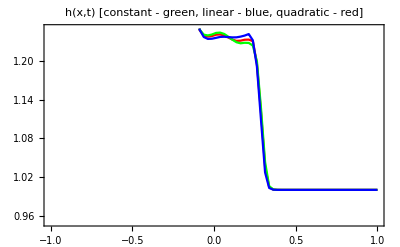
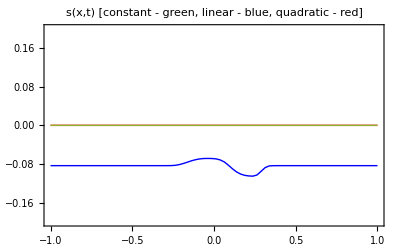
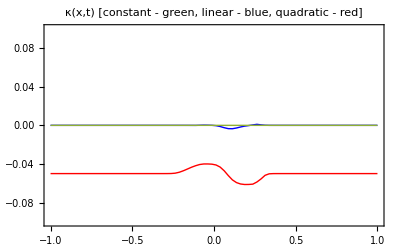
-Graphics- | 
 | 
-Graphics- | -Graphics-

```mathematica
p={{-0.4,0.25},{0.0,0.25},{0.4,0.25}};
Grid[{{
Plot[{hQ[x],hL[x],hSW[x]},{x,x1,x2},
PlotRange->{{x1,x2},{0.95,1.25}},PlotStyle->color⟦1;;3⟧,PlotLabel->"h(x,t) [constant - green, linear - blue, quadratic - red]",
ImageSize->iSize,Frame->True]
},{
LocatorPane[Dynamic[p],
Dynamic[
Plot[{uMeanQ[x],uMeanL[x],uMeanSW[x]},{x,x1,x2},PlotRange->{{x1,x2},{0.05,0.45}},PlotStyle->color⟦1;;3⟧,
PlotLabel->"u_m(x,t) [constant - green, linear - blue, quadratic - red]",ImageSize->iSize,Frame->True,
Epilog->{PointSize[0.03],color⟦1⟧,Point[{p⟦1,1⟧,uMeanQ[p⟦1,1⟧]}],color⟦2⟧,Point[{p⟦2,1⟧,uMeanL[p⟦2,1⟧]}],color⟦3⟧,Point[{p⟦3,1⟧,uMeanSW[p⟦3,1⟧]}]}]],Appearance->None],
Dynamic[
ParametricPlot[Evaluate[{{uFullQ[p⟦1,1⟧,y],y},{uFullL[p⟦2,1⟧,y],y},{uFullSW[p⟦3,1⟧,y],y}}],{y,y1,y2},AspectRatio->0.5,PlotRange->{{-0.15,0.65},{0,1}},PlotStyle->color⟦1;;3⟧,
PlotLabel->"velocity profiles [intial velocity - thin]",Frame->True,ImageSize->1.2iSize]]
},{
Plot[{sQ[x],sL[x],sSW[x]},{x,x1,x2},
PlotRange->{{x1,x2},{-0.2,0.2}},PlotStyle->{{Thick,Red},{Thick,Blue},Thin},PlotLabel->"s(x,t) [constant - green, linear - blue, quadratic - red]",
ImageSize->iSize,Frame->True],
Plot[{κQ[x],κL[x],κSW[x]},{x,x1,x2},
PlotRange->{{x1,x2},{-0.1,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue},Thin},PlotLabel->"κ(x,t) [constant - green, linear - blue, quadratic - red]",
ImageSize->iSize,Frame->True]
}},
Alignment->{{Right,Left},{Right,Left},{Right,Left}}
]
```

### "Open/Close" Depth-Projected Shallow Flow (friction, linear / moderate quadratic /small quadratic profiles)

```mathematica
u0[x_,y_]=0.5y;
```

```mathematica
(*χ=10^6;
R=0.01;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=1;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
```

```mathematica
(*χ=10^6;
R=0.1;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=2;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
```

```mathematica
χ=0.1;
R=0.1;
u0[x_,y_]:=0.04+0.02*y;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=1;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}];
```

```mathematica
dataset=Flatten[Referencevalues];
Export["damBreak-and-smooth_linear_lambda0.1_nu0.1_t5_adaptiveOrder.txt",dataset,"CSV"]
```

```mathematica
χ=0.1;
R=0.1;
(*u0[x_,y_]=0.25-2.5*y+7.5*y^2-5*y^3;*)
u0[x_,y_]=0;
FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=2;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{0.03125,5.,0.,0.,0.},{0.09375,5.,0.,0.,0.},{0.15625,5.,0.,0.,0.},{0.21875,5.,0.,0.,0.},{0.28125,5.,0.,0.,0.},{0.34375,5.,0.,0.,0.},{0.40625,5.,0.,0.,0.},{0.46875,5.,0.,0.,0.},{0.53125,5.,0.,0.,0.},{0.59375,5.,0.,0.,0.},{0.65625,5.,0.,0.,0.},{0.71875,5.,0.,0.,0.},{0.78125,5.,0.,0.,0.},{0.84375,5.,0.,0.,0.},{0.90625,5.,0.,0.,0.},{0.96875,5.,0.,0.,0.},{1.03125,5.,0.,0.,0.},{1.09375,5.,0.,0.,0.},{1.15625,5.,0.,0.,0.},{1.21875,5.,0.,0.,0.},{1.28125,5.,0.,0.,0.},{1.34375,5.,0.,0.,0.},{1.40625,5.,0.,0.,0.},{1.46875,5.,0.,0.,0.},{1.53125,5.,0.,0.,0.},{1.59375,5.,5.09003×10^-16,-1.28608×10^-18,-1.23958×10^-18},{1.65625,5.,4.38527×10^-15,-1.35554×10^-17,-1.29888×10^-17},{1.71875,5.,3.10647×10^-14,-9.9627×10^-17,-9.54355×10^-17},{1.78125,5.,2.09539×10^-13,-6.88436×10^-16,-6.58855×10^-16},{1.84375,5.,1.40112×10^-12,-4.62465×10^-15,-4.42567×10^-15},{1.90625,5.,9.22766×10^-12,-3.05832×10^-14,-2.92647×10^-14},{1.96875,5.,6.00631×10^-11,-1.999×10^-13,-1.91269×10^-13},{2.03125,5.,3.85504×10^-10,-1.28853×10^-12,-1.2328×10^-12},{2.09375,5.,2.44363×10^-9,-8.19933×10^-12,-7.84409×10^-12},{2.15625,5.,1.53219×10^-8,-5.15849×10^-11,-4.93467×10^-11},{2.21875,5.,9.51816×10^-8,-3.21376×10^-10,-3.07415×10^-10},{2.28125,5.,5.86747×10^-7,-1.98585×10^-9,-1.89949×10^-9},{2.34375,4.99999,3.59439×10^-6,-1.21888×10^-8,-1.16582×10^-8},{2.40625,4.99995,0.0000219075,-7.43918×10^-8,-7.11521×10^-8},{2.46875,4.9997,0.000133092,-4.51504×10^-7,-4.31858×10^-7},{2.53125,4.99819,0.000809735,-2.72496×10^-6,-2.60742×10^-6},{2.59375,4.98941,0.00472569,-0.0000154899,-0.0000148453},{2.65625,4.96312,0.0164863,-0.0000647474,-0.0000618805},{2.71875,4.92064,0.0355142,-0.000175021,-0.000166445},{2.78125,4.86552,0.0603179,-0.00035919,-0.000339789},{2.84375,4.80114,0.0894413,-0.000626994,-0.000589943},{2.90625,4.73069,0.121492,-0.000982144,-0.000919145},{2.96875,4.6565,0.155465,-0.00142621,-0.00132755},{3.03125,4.58016,0.190672,-0.00195936,-0.00181401},{3.09375,4.50262,0.226683,-0.00258122,-0.00237685},{3.15625,4.42449,0.263235,-0.00329154,-0.00301455},{3.21875,4.34614,0.300157,-0.00409015,-0.00372562},{3.28125,4.26783,0.337343,-0.00497705,-0.00450878},{3.34375,4.18971,0.37472,-0.00595251,-0.00536292},{3.40625,4.1119,0.412233,-0.00701711,-0.0062872},{3.46875,4.0345,0.449839,-0.0081717,-0.00728095},{3.53125,3.95758,0.487506,-0.00941737,-0.00834368},{3.59375,3.88118,0.525206,-0.0107554,-0.00947498},{3.65625,3.80535,0.562917,-0.0121873,-0.0106745},{3.71875,3.73014,0.600619,-0.0137146,-0.011942},{3.78125,3.65557,0.638295,-0.0153392,-0.0132772},{3.84375,3.58165,0.67593,-0.0170631,-0.0146799},{3.90625,3.50843,0.713509,-0.0188885,-0.0161502},{3.96875,3.43591,0.751022,-0.0208178,-0.0176877},{4.03125,3.36411,0.788455,-0.0228536,-0.0192925},{4.09375,3.29305,0.825793,-0.0249988,-0.0209646},{4.15625,3.22276,0.863013,-0.0272545,-0.0227022},{4.21875,3.1533,0.90008,-0.0296201,-0.0245022},{4.28125,3.08476,0.936937,-0.0321132,-0.0263761},{4.34375,3.01722,0.973506,-0.034733,-0.0283201},{4.40625,2.95107,1.00958,-0.0374763,-0.0303265},{4.46875,2.88696,1.04475,-0.0403602,-0.0324054},{4.53125,2.82602,1.07831,-0.0433997,-0.0345621},{4.59375,2.76991,1.10921,-0.0466229,-0.03681},{4.65625,2.7208,1.13609,-0.0500582,-0.0391594},{4.71875,2.68092,1.15749,-0.0537354,-0.0416184},{4.78125,2.65171,1.17244,-0.0576616,-0.0441757},{4.84375,2.63281,1.18108,-0.0617883,-0.0467813},{4.90625,2.62174,1.18494,-0.0659944,-0.0493419},{4.96875,2.61469,1.18639,-0.0701178,-0.0517481},{5.03125,2.60818,1.18762,-0.0740248,-0.0539226},{5.09375,2.60035,1.18978,-0.0776691,-0.0558539},{5.15625,2.59105,1.19294,-0.0810897,-0.0575863},{5.21875,2.58107,1.19658,-0.0843712,-0.0591849},{5.28125,2.57127,1.20014,-0.0876,-0.0607061},{5.34375,2.56219,1.20325,-0.0908338,-0.0621858},{5.40625,2.55399,1.20582,-0.0940913,-0.0636315},{5.46875,2.54658,1.2079,-0.097338,-0.0650215},{5.53125,2.53988,1.20961,-0.100485,-0.0663031},{5.59375,2.53379,1.21104,-0.103386,-0.0673935},{5.65625,2.52822,1.21228,-0.105842,-0.0681976},{5.71875,2.52365,1.21348,-0.107552,-0.0686612},{5.78125,2.51904,1.21455,-0.108481,-0.0688452},{5.84375,2.51502,1.21566,-0.108932,-0.0688312},{5.90625,2.51149,1.21676,-0.108807,-0.0686031},{5.96875,2.50846,1.21772,-0.107823,-0.0680182},{6.03125,2.5061,1.21855,-0.106059,-0.0671419},{6.09375,2.50426,1.2192,-0.103695,-0.0660708},{6.15625,2.50285,1.21966,-0.100858,-0.0648462},{6.21875,2.50181,1.2199,-0.0976273,-0.0634795},{6.28125,2.50102,1.21998,-0.0940529,-0.0619645},{6.34375,2.50022,1.22003,-0.0901673,-0.0602879},{6.40625,2.49911,1.22024,-0.0859912,-0.0584341},{6.46875,2.49745,1.22065,-0.0815295,-0.056384},{6.53125,2.4952,1.22123,-0.0767614,-0.0541071},{6.59375,2.49251,1.22199,-0.0716551,-0.0515648},{6.65625,2.48991,1.22289,-0.0662065,-0.0487309},{6.71875,2.48701,1.22323,-0.0603879,-0.0455721},{6.78125,2.48243,1.22254,-0.0542232,-0.0420716},{6.84375,2.47918,1.22174,-0.047732,-0.0381697},{6.90625,2.48253,1.22484,-0.0410555,-0.0338827},{6.96875,2.48054,1.22923,-0.0342233,-0.0294553},{7.03125,2.28859,1.11678,-0.0209037,-0.0200983},{7.09375,1.53787,0.552061,-0.00746809,-0.00768272},{7.15625,1.04553,0.0474892,-0.000704246,-0.000636947},{7.21875,1.00176,0.00174963,-0.0000271509,-0.0000231626},{7.28125,1.00006,0.0000591812,-8.92993×10^-7,-7.48385×10^-7},{7.34375,1.,1.91129×10^-6,-2.83104×10^-8,-2.36245×10^-8},{7.40625,1.,6.27225×10^-8,-9.32616×10^-10,-7.76969×10^-10},{7.46875,1.,2.0799×10^-9,-3.09486×10^-11,-2.57726×10^-11},{7.53125,1.,6.88988×10^-11,-1.02399×10^-12,-8.52701×10^-13},{7.59375,1.,2.27377×10^-12,-3.37469×10^-14,-2.81027×10^-14},{7.65625,1.,7.46992×10^-14,-1.10604×10^-15,-9.21515×10^-16},{7.71875,1.,2.41154×10^-15,-3.48532×10^-17,-2.90586×10^-17},{7.78125,1.,5.53436×10^-17,-1.46586×10^-18,-1.17516×10^-18},{7.84375,1.,0.,0.,0.},{7.90625,1.,0.,0.,0.},{7.96875,1.,0.,0.,0.},{8.03125,1.,0.,0.,0.},{8.09375,1.,0.,0.,0.},{8.15625,1.,0.,0.,0.},{8.21875,1.,0.,0.,0.},{8.28125,1.,0.,0.,0.},{8.34375,1.,0.,0.,0.},{8.40625,1.,0.,0.,0.},{8.46875,1.,0.,0.,0.},{8.53125,1.,0.,0.,0.},{8.59375,1.,0.,0.,0.},{8.65625,1.,0.,0.,0.},{8.71875,1.,0.,0.,0.},{8.78125,1.,0.,0.,0.},{8.84375,1.,0.,0.,0.},{8.90625,1.,0.,0.,0.},{8.96875,1.,0.,0.,0.},{9.03125,1.,0.,0.,0.},{9.09375,1.,0.,0.,0.},{9.15625,1.,0.,0.,0.},{9.21875,1.,0.,0.,0.},{9.28125,1.,0.,0.,0.},{9.34375,1.,0.,0.,0.},{9.40625,1.,0.,0.,0.},{9.46875,1.,0.,0.,0.},{9.53125,1.,0.,0.,0.},{9.59375,1.,0.,0.,0.},{9.65625,1.,0.,0.,0.},{9.71875,1.,0.,0.,0.},{9.78125,1.,0.,0.,0.},{9.84375,1.,0.,0.,0.},{9.90625,1.,0.,0.,0.},{9.96875,1.,0.,0.,0.}}

```mathematica
(*u0[x_,y_]=0.15 +0.6y(1-y);*)
u0[x_,y_]=0.25-2.5*y+7.5*y^2-5*y^3;

χ=0.1;
R=0.1;
FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=3;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];
Referencevalues=Table[{xs[i],Hraw[[i,1]],Map[Mean,Uraw][[i]],Map[sMean.#&,Uraw][[i]],Map[κMean.#&,Uraw][[i]]},{i,1,nx}]
```

{{10.0125,5.,0.247636,-0.0855805,-0.00213159},{10.0375,5.,0.247636,-0.0855805,-0.00213159},{10.0625,5.,0.247636,-0.0855805,-0.00213159},{10.0875,5.,0.247636,-0.0855805,-0.00213159},{10.1125,5.,0.247636,-0.0855805,-0.00213159},{10.1375,5.,0.247636,-0.0855805,-0.00213159},{10.1625,5.,0.247636,-0.0855805,-0.00213159},{10.1875,5.,0.247636,-0.0855805,-0.00213159},{10.2125,5.,0.247636,-0.0855805,-0.00213159},{10.2375,5.,0.247636,-0.0855805,-0.00213159},{10.2625,5.,0.247636,-0.0855805,-0.00213159},{10.2875,5.,0.247636,-0.0855805,-0.00213159},{10.3125,5.,0.247636,-0.0855805,-0.00213159},{10.3375,5.,0.247636,-0.0855805,-0.00213159},{10.3625,5.,0.247636,-0.0855805,-0.00213159},{10.3875,5.,0.247636,-0.0855805,-0.00213159},{10.4125,5.,0.247636,-0.0855805,-0.00213159},{10.4375,5.,0.247636,-0.0855805,-0.00213159},{10.4625,5.,0.247636,-0.0855805,-0.00213159},{10.4875,5.,0.247636,-0.0855805,-0.00213159},{10.5125,5.,0.247636,-0.0855805,-0.00213159},{10.5375,5.,0.247636,-0.0855805,-0.00213159},{10.5625,5.,0.247636,-0.0855805,-0.00213159},{10.5875,5.,0.247636,-0.0855805,-0.00213159},{10.6125,5.,0.247636,-0.0855805,-0.00213159},{10.6375,5.,0.247636,-0.0855805,-0.00213159},{10.6625,5.,0.247636,-0.0855805,-0.00213159},{10.6875,5.,0.247636,-0.0855805,-0.00213159},{10.7125,5.,0.247636,-0.0855805,-0.00213159},{10.7375,5.,0.247636,-0.0855805,-0.00213159},{10.7625,5.,0.247636,-0.0855805,-0.00213159},{10.7875,5.,0.247636,-0.0855805,-0.00213159},{10.8125,5.,0.247636,-0.0855805,-0.00213159},{10.8375,5.,0.247636,-0.0855805,-0.00213159},{10.8625,5.,0.247636,-0.0855805,-0.00213159},{10.8875,5.,0.247636,-0.0855805,-0.00213159},{10.9125,5.,0.247636,-0.0855805,-0.00213159},{10.9375,5.,0.247636,-0.0855805,-0.00213159},{10.9625,5.,0.247636,-0.0855805,-0.00213159},{10.9875,5.,0.247636,-0.0855805,-0.00213159},{11.0125,5.,0.247636,-0.0855805,-0.00213159},{11.0375,5.,0.247636,-0.0855805,-0.00213159},{11.0625,5.,0.247636,-0.0855805,-0.00213159},{11.0875,5.,0.247636,-0.0855805,-0.00213159},{11.1125,5.,0.247636,-0.0855805,-0.00213159},{11.1375,5.,0.247636,-0.0855805,-0.00213159},{11.1625,5.,0.247636,-0.0855805,-0.00213159},{11.1875,5.,0.247636,-0.0855805,-0.00213159},{11.2125,5.,0.247636,-0.0855805,-0.00213159},{11.2375,5.,0.247636,-0.0855805,-0.00213159},{11.2625,5.,0.247636,-0.0855805,-0.00213159},{11.2875,5.,0.247636,-0.0855805,-0.00213159},{11.3125,5.,0.247636,-0.0855805,-0.00213159},{11.3375,5.,0.247636,-0.0855805,-0.00213159},{11.3625,5.,0.247636,-0.0855805,-0.00213159},{11.3875,5.,0.247636,-0.0855805,-0.00213159},{11.4125,5.,0.247636,-0.0855805,-0.00213159},{11.4375,5.,0.247636,-0.0855805,-0.00213159},{11.4625,5.,0.247636,-0.0855805,-0.00213159},{11.4875,5.,0.247636,-0.0855805,-0.00213159},{11.5125,5.,0.247636,-0.0855805,-0.00213159},{11.5375,5.,0.247636,-0.0855805,-0.00213159},{11.5625,5.,0.247636,-0.0855805,-0.00213159},{11.5875,5.,0.247636,-0.0855805,-0.00213159},{11.6125,5.,0.247636,-0.0855805,-0.00213159},{11.6375,5.,0.247636,-0.0855805,-0.00213159},{11.6625,5.,0.247636,-0.0855805,-0.00213159},{11.6875,5.,0.247636,-0.0855805,-0.00213159},{11.7125,5.,0.247636,-0.0855805,-0.00213159},{11.7375,5.,0.247636,-0.0855805,-0.00213159},{11.7625,5.,0.247636,-0.0855805,-0.00213159},{11.7875,5.,0.247636,-0.0855805,-0.00213159},{11.8125,5.,0.247636,-0.0855805,-0.00213159},{11.8375,5.,0.247636,-0.0855805,-0.00213159},{11.8625,5.,0.247636,-0.0855805,-0.00213159},{11.8875,5.,0.247636,-0.0855805,-0.00213159},{11.9125,5.,0.247636,-0.0855805,-0.00213159},{11.9375,5.,0.247636,-0.0855805,-0.00213159},{11.9625,5.,0.247636,-0.0855805,-0.00213159},{11.9875,5.,0.247636,-0.0855805,-0.00213159},{12.0125,5.,0.247636,-0.0855805,-0.00213159},{12.0375,5.,0.247636,-0.0855805,-0.00213159},{12.0625,5.,0.247636,-0.0855805,-0.00213159},{12.0875,5.,0.247636,-0.0855805,-0.00213159},{12.1125,5.,0.247636,-0.0855805,-0.00213159},{12.1375,5.,0.247636,-0.0855805,-0.00213159},{12.1625,5.,0.247636,-0.0855805,-0.00213159},{12.1875,5.,0.247636,-0.0855805,-0.00213159},{12.2125,5.,0.247636,-0.0855805,-0.00213159},{12.2375,5.,0.247636,-0.0855805,-0.00213159},{12.2625,5.,0.247636,-0.0855805,-0.00213159},{12.2875,5.,0.247636,-0.0855805,-0.00213159},{12.3125,5.,0.247636,-0.0855805,-0.00213159},{12.3375,5.,0.247636,-0.0855805,-0.00213159},{12.3625,5.,0.247636,-0.0855805,-0.00213159},{12.3875,5.,0.247636,-0.0855805,-0.00213159},{12.4125,5.,0.247636,-0.0855805,-0.00213159},{12.4375,5.,0.247636,-0.0855805,-0.00213159},{12.4625,5.,0.247636,-0.0855805,-0.00213159},{12.4875,5.,0.247636,-0.0855805,-0.00213159},{12.5125,5.,0.247636,-0.0855805,-0.00213159},{12.5375,5.,0.247636,-0.0855805,-0.00213159},{12.5625,5.,0.247636,-0.0855805,-0.00213159},{12.5875,5.,0.247636,-0.0855805,-0.00213159},{12.6125,5.,0.247636,-0.0855805,-0.00213159},{12.6375,5.,0.247636,-0.0855805,-0.00213159},{12.6625,5.,0.247636,-0.0855805,-0.00213159},{12.6875,5.,0.247636,-0.0855805,-0.00213159},{12.7125,5.,0.247636,-0.0855805,-0.00213159},{12.7375,5.,0.247636,-0.0855805,-0.00213159},{12.7625,5.,0.247636,-0.0855805,-0.00213159},{12.7875,5.,0.247636,-0.0855805,-0.00213159},{12.8125,5.,0.247636,-0.0855805,-0.00213159},{12.8375,5.,0.247636,-0.0855805,-0.00213159},{12.8625,5.,0.247636,-0.0855805,-0.00213159},{12.8875,5.,0.247636,-0.0855805,-0.00213159},{12.9125,5.,0.247636,-0.0855805,-0.00213159},{12.9375,5.,0.247636,-0.0855805,-0.00213159},{12.9625,5.,0.247636,-0.0855805,-0.00213159},{12.9875,5.,0.247636,-0.0855805,-0.00213159},{13.0125,5.,0.247636,-0.0855805,-0.00213159},{13.0375,5.,0.247636,-0.0855805,-0.00213159},{13.0625,5.,0.247636,-0.0855805,-0.00213159},{13.0875,5.,0.247636,-0.0855805,-0.00213159},{13.1125,5.,0.247636,-0.0855805,-0.00213159},{13.1375,5.,0.247636,-0.0855805,-0.00213159},{13.1625,5.,0.247636,-0.0855805,-0.00213159},{13.1875,5.,0.247636,-0.0855805,-0.00213159},{13.2125,5.,0.247636,-0.0855805,-0.00213159},{13.2375,5.,0.247636,-0.0855805,-0.00213159},{13.2625,5.,0.247636,-0.0855805,-0.00213159},{13.2875,5.,0.247636,-0.0855805,-0.00213159},{13.3125,5.,0.247636,-0.0855805,-0.00213159},{13.3375,5.,0.247636,-0.0855805,-0.00213159},{13.3625,5.,0.247636,-0.0855805,-0.00213159},{13.3875,5.,0.247636,-0.0855805,-0.00213159},{13.4125,5.,0.247636,-0.0855805,-0.00213159},{13.4375,5.,0.247636,-0.0855805,-0.00213159},{13.4625,5.,0.247636,-0.0855805,-0.00213159},{13.4875,5.,0.247636,-0.0855805,-0.00213159},{13.5125,5.,0.247636,-0.0855805,-0.00213159},{13.5375,5.,0.247636,-0.0855805,-0.00213159},{13.5625,5.,0.247636,-0.0855805,-0.00213159},{13.5875,5.,0.247636,-0.0855805,-0.00213159},{13.6125,5.,0.247636,-0.0855805,-0.00213159},{13.6375,4.99999,0.247639,-0.0855804,-0.0021316},{13.6625,4.99995,0.247659,-0.0855797,-0.00213171},{13.6875,4.99966,0.24779,-0.0855755,-0.00213245},{13.7125,4.9979,0.248581,-0.0855493,-0.00213698},{13.7375,4.98789,0.253089,-0.0853967,-0.00216329},{13.7625,4.93607,0.276419,-0.084574,-0.00230359},{13.7875,4.8077,0.335178,-0.0824997,-0.0026815},{13.8125,4.61169,0.425865,-0.079439,-0.00331347},{13.8375,4.37345,0.538711,-0.0758246,-0.00416885},{13.8625,4.11502,0.664636,-0.0720707,-0.00522248},{13.8875,3.8497,0.797515,-0.0684287,-0.0064612},{13.9125,3.58538,0.934446,-0.0650758,-0.00785082},{13.9375,3.32705,1.07385,-0.0623325,-0.00932066},{13.9625,3.07868,1.21179,-0.0606382,-0.0112731},{13.9875,2.84784,1.34207,-0.0587459,-0.0140786},{14.0125,2.66136,1.45614,-0.056403,-0.0168022},{14.0375,2.54828,1.52614,-0.057746,-0.0190823},{14.0625,2.51461,1.5432,-0.062513,-0.0218831},{14.0875,2.5168,1.53636,-0.0694295,-0.0244675},{14.1125,2.53086,1.51635,-0.0849354,-0.025575},{14.1375,2.54436,1.49935,-0.119726,-0.0253032},{14.1625,2.54831,1.49209,-0.167984,-0.0331059},{14.1875,2.46668,1.49002,-0.209914,-0.0491818},{14.2125,2.26051,1.47897,-0.247504,-0.0778206},{14.2375,1.74224,1.11006,-0.204698,-0.0867365},{14.2625,1.13138,0.41025,-0.107027,-0.0211294},{14.2875,1.00709,0.251021,-0.085117,-0.00430153},{14.3125,1.00032,0.243499,-0.0841576,-0.00381421},{14.3375,1.00001,0.243171,-0.0841188,-0.00380075},{14.3625,1.,0.243156,-0.0841171,-0.00380028},{14.3875,1.,0.243155,-0.084117,-0.00380026},{14.4125,1.,0.243155,-0.084117,-0.00380026},{14.4375,1.,0.243155,-0.084117,-0.00380026},{14.4625,1.,0.243155,-0.084117,-0.00380026},{14.4875,1.,0.243155,-0.084117,-0.00380026},{14.5125,1.,0.243155,-0.084117,-0.00380026},{14.5375,1.,0.243155,-0.084117,-0.00380026},{14.5625,1.,0.243155,-0.084117,-0.00380026},{14.5875,1.,0.243155,-0.084117,-0.00380026},{14.6125,1.,0.243155,-0.084117,-0.00380026},{14.6375,1.,0.243155,-0.084117,-0.00380026},{14.6625,1.,0.243155,-0.084117,-0.00380026},{14.6875,1.,0.243155,-0.084117,-0.00380026},{14.7125,1.,0.243155,-0.084117,-0.00380026},{14.7375,1.,0.243155,-0.084117,-0.00380026},{14.7625,1.,0.243155,-0.084117,-0.00380026},{14.7875,1.,0.243155,-0.084117,-0.00380026},{14.8125,1.,0.243155,-0.084117,-0.00380026},{14.8375,1.,0.243155,-0.084117,-0.00380026},{14.8625,1.,0.243155,-0.084117,-0.00380026},{14.8875,1.,0.243155,-0.084117,-0.00380026},{14.9125,1.,0.243155,-0.084117,-0.00380026},{14.9375,1.,0.243155,-0.084117,-0.00380026},{14.9625,1.,0.243155,-0.084117,-0.00380026},{14.9875,1.,0.243155,-0.084117,-0.00380026},{15.0125,1.,0.243155,-0.084117,-0.00380026},{15.0375,1.,0.243155,-0.084117,-0.00380026},{15.0625,1.,0.243155,-0.084117,-0.00380026},{15.0875,1.,0.243155,-0.084117,-0.00380026},{15.1125,1.,0.243155,-0.084117,-0.00380026},{15.1375,1.,0.243155,-0.084117,-0.00380026},{15.1625,1.,0.243155,-0.084117,-0.00380026},{15.1875,1.,0.243155,-0.084117,-0.00380026},{15.2125,1.,0.243155,-0.084117,-0.00380026},{15.2375,1.,0.243155,-0.084117,-0.00380026},{15.2625,1.,0.243155,-0.084117,-0.00380026},{15.2875,1.,0.243155,-0.084117,-0.00380026},{15.3125,1.,0.243155,-0.084117,-0.00380026},{15.3375,1.,0.243155,-0.084117,-0.00380026},{15.3625,1.,0.243155,-0.084117,-0.00380026},{15.3875,1.,0.243155,-0.084117,-0.00380026},{15.4125,1.,0.243155,-0.084117,-0.00380026},{15.4375,1.,0.243155,-0.084117,-0.00380026},{15.4625,1.,0.243155,-0.084117,-0.00380026},{15.4875,1.,0.243155,-0.084117,-0.00380026},{15.5125,1.,0.243155,-0.084117,-0.00380026},{15.5375,1.,0.243155,-0.084117,-0.00380026},{15.5625,1.,0.243155,-0.084117,-0.00380026},{15.5875,1.,0.243155,-0.084117,-0.00380026},{15.6125,1.,0.243155,-0.084117,-0.00380026},{15.6375,1.,0.243155,-0.084117,-0.00380026},{15.6625,1.,0.243155,-0.084117,-0.00380026},{15.6875,1.,0.243155,-0.084117,-0.00380026},{15.7125,1.,0.243155,-0.084117,-0.00380026},{15.7375,1.,0.243155,-0.084117,-0.00380026},{15.7625,1.,0.243155,-0.084117,-0.00380026},{15.7875,1.,0.243155,-0.084117,-0.00380026},{15.8125,1.,0.243155,-0.084117,-0.00380026},{15.8375,1.,0.243155,-0.084117,-0.00380026},{15.8625,1.,0.243155,-0.084117,-0.00380026},{15.8875,1.,0.243155,-0.084117,-0.00380026},{15.9125,1.,0.243155,-0.084117,-0.00380026},{15.9375,1.,0.243155,-0.084117,-0.00380026},{15.9625,1.,0.243155,-0.084117,-0.00380026},{15.9875,1.,0.243155,-0.084117,-0.00380026},{16.0125,1.,0.243155,-0.084117,-0.00380026},{16.0375,1.,0.243155,-0.084117,-0.00380026},{16.0625,1.,0.243155,-0.084117,-0.00380026},{16.0875,1.,0.243155,-0.084117,-0.00380026},{16.1125,1.,0.243155,-0.084117,-0.00380026},{16.1375,1.,0.243155,-0.084117,-0.00380026},{16.1625,1.,0.243155,-0.084117,-0.00380026},{16.1875,1.,0.243155,-0.084117,-0.00380026},{16.2125,1.,0.243155,-0.084117,-0.00380026},{16.2375,1.,0.243155,-0.084117,-0.00380026},{16.2625,1.,0.243155,-0.084117,-0.00380026},{16.2875,1.,0.243155,-0.084117,-0.00380026},{16.3125,1.,0.243155,-0.084117,-0.00380026},{16.3375,1.,0.243155,-0.084117,-0.00380026},{16.3625,1.,0.243155,-0.084117,-0.00380026},{16.3875,1.,0.243155,-0.084117,-0.00380026},{16.4125,1.,0.243155,-0.084117,-0.00380026},{16.4375,1.,0.243155,-0.084117,-0.00380026},{16.4625,1.,0.243155,-0.084117,-0.00380026},{16.4875,1.,0.243155,-0.084117,-0.00380026},{16.5125,1.,0.243155,-0.084117,-0.00380026},{16.5375,1.,0.243155,-0.084117,-0.00380026},{16.5625,1.,0.243155,-0.084117,-0.00380026},{16.5875,1.,0.243155,-0.084117,-0.00380026},{16.6125,1.,0.243155,-0.084117,-0.00380026},{16.6375,1.,0.243155,-0.084117,-0.00380026},{16.6625,1.,0.243155,-0.084117,-0.00380026},{16.6875,1.,0.243155,-0.084117,-0.00380026},{16.7125,1.,0.243155,-0.084117,-0.00380026},{16.7375,1.,0.243155,-0.084117,-0.00380026},{16.7625,1.,0.243155,-0.084117,-0.00380026},{16.7875,1.,0.243155,-0.084117,-0.00380026},{16.8125,1.,0.243155,-0.084117,-0.00380026},{16.8375,1.,0.243155,-0.084117,-0.00380026},{16.8625,1.,0.243155,-0.084117,-0.00380026},{16.8875,1.,0.243155,-0.084117,-0.00380026},{16.9125,1.,0.243155,-0.084117,-0.00380026},{16.9375,1.,0.243155,-0.084117,-0.00380026},{16.9625,1.,0.243155,-0.084117,-0.00380026},{16.9875,1.,0.243155,-0.084117,-0.00380026},{17.0125,1.,0.243155,-0.084117,-0.00380026},{17.0375,1.,0.243155,-0.084117,-0.00380026},{17.0625,1.,0.243155,-0.084117,-0.00380026},{17.0875,1.,0.243155,-0.084117,-0.00380026},{17.1125,1.,0.243155,-0.084117,-0.00380026},{17.1375,1.,0.243155,-0.084117,-0.00380026},{17.1625,1.,0.243155,-0.084117,-0.00380026},{17.1875,1.,0.243155,-0.084117,-0.00380026},{17.2125,1.,0.243155,-0.084117,-0.00380026},{17.2375,1.,0.243155,-0.084117,-0.00380026},{17.2625,1.,0.243155,-0.084117,-0.00380026},{17.2875,1.,0.243155,-0.084117,-0.00380026},{17.3125,1.,0.243155,-0.084117,-0.00380026},{17.3375,1.,0.243155,-0.084117,-0.00380026},{17.3625,1.,0.243155,-0.084117,-0.00380026},{17.3875,1.,0.243155,-0.084117,-0.00380026},{17.4125,1.,0.243155,-0.084117,-0.00380026},{17.4375,1.,0.243155,-0.084117,-0.00380026},{17.4625,1.,0.243155,-0.084117,-0.00380026},{17.4875,1.,0.243155,-0.084117,-0.00380026},{17.5125,1.,0.243155,-0.084117,-0.00380026},{17.5375,1.,0.243155,-0.084117,-0.00380026},{17.5625,1.,0.243155,-0.084117,-0.00380026},{17.5875,1.,0.243155,-0.084117,-0.00380026},{17.6125,1.,0.243155,-0.084117,-0.00380026},{17.6375,1.,0.243155,-0.084117,-0.00380026},{17.6625,1.,0.243155,-0.084117,-0.00380026},{17.6875,1.,0.243155,-0.084117,-0.00380026},{17.7125,1.,0.243155,-0.084117,-0.00380026},{17.7375,1.,0.243155,-0.084117,-0.00380026},{17.7625,1.,0.243155,-0.084117,-0.00380026},{17.7875,1.,0.243155,-0.084117,-0.00380026},{17.8125,1.,0.243155,-0.084117,-0.00380026},{17.8375,1.,0.243155,-0.084117,-0.00380026},{17.8625,1.,0.243155,-0.084117,-0.00380026},{17.8875,1.,0.243155,-0.084117,-0.00380026},{17.9125,1.,0.243155,-0.084117,-0.00380026},{17.9375,1.,0.243155,-0.084117,-0.00380026},{17.9625,1.,0.243155,-0.084117,-0.00380026},{17.9875,1.,0.243155,-0.084117,-0.00380026},{18.0125,1.,0.243155,-0.084117,-0.00380026},{18.0375,1.,0.243155,-0.084117,-0.00380026},{18.0625,1.,0.243155,-0.084117,-0.00380026},{18.0875,1.,0.243155,-0.084117,-0.00380026},{18.1125,1.,0.243155,-0.084117,-0.00380026},{18.1375,1.,0.243155,-0.084117,-0.00380026},{18.1625,1.,0.243155,-0.084117,-0.00380026},{18.1875,1.,0.243155,-0.084117,-0.00380026},{18.2125,1.,0.243155,-0.084117,-0.00380026},{18.2375,1.,0.243155,-0.084117,-0.00380026},{18.2625,1.,0.243155,-0.084117,-0.00380026},{18.2875,1.,0.243155,-0.084117,-0.00380026},{18.3125,1.,0.243155,-0.084117,-0.00380026},{18.3375,1.,0.243155,-0.084117,-0.00380026},{18.3625,1.,0.243155,-0.084117,-0.00380026},{18.3875,1.,0.243155,-0.084117,-0.00380026},{18.4125,1.,0.243155,-0.084117,-0.00380026},{18.4375,1.,0.243155,-0.084117,-0.00380026},{18.4625,1.,0.243155,-0.084117,-0.00380026},{18.4875,1.,0.243155,-0.084117,-0.00380026},{18.5125,1.,0.243155,-0.084117,-0.00380026},{18.5375,1.,0.243155,-0.084117,-0.00380026},{18.5625,1.,0.243155,-0.084117,-0.00380026},{18.5875,1.,0.243155,-0.084117,-0.00380026},{18.6125,1.,0.243155,-0.084117,-0.00380026},{18.6375,1.,0.243155,-0.084117,-0.00380026},{18.6625,1.,0.243155,-0.084117,-0.00380026},{18.6875,1.,0.243155,-0.084117,-0.00380026},{18.7125,1.,0.243155,-0.084117,-0.00380026},{18.7375,1.,0.243155,-0.084117,-0.00380026},{18.7625,1.,0.243155,-0.084117,-0.00380026},{18.7875,1.,0.243155,-0.084117,-0.00380026},{18.8125,1.,0.243155,-0.084117,-0.00380026},{18.8375,1.,0.243155,-0.084117,-0.00380026},{18.8625,1.,0.243155,-0.084117,-0.00380026},{18.8875,1.,0.243155,-0.084117,-0.00380026},{18.9125,1.,0.243155,-0.084117,-0.00380026},{18.9375,1.,0.243155,-0.084117,-0.00380026},{18.9625,1.,0.243155,-0.084117,-0.00380026},{18.9875,1.,0.243155,-0.084117,-0.00380026},{19.0125,1.,0.243155,-0.084117,-0.00380026},{19.0375,1.,0.243155,-0.084117,-0.00380026},{19.0625,1.,0.243155,-0.084117,-0.00380026},{19.0875,1.,0.243155,-0.084117,-0.00380026},{19.1125,1.,0.243155,-0.084117,-0.00380026},{19.1375,1.,0.243155,-0.084117,-0.00380026},{19.1625,1.,0.243155,-0.084117,-0.00380026},{19.1875,1.,0.243155,-0.084117,-0.00380026},{19.2125,1.,0.243155,-0.084117,-0.00380026},{19.2375,1.,0.243155,-0.084117,-0.00380026},{19.2625,1.,0.243155,-0.084117,-0.00380026},{19.2875,1.,0.243155,-0.084117,-0.00380026},{19.3125,1.,0.243155,-0.084117,-0.00380026},{19.3375,1.,0.243155,-0.084117,-0.00380026},{19.3625,1.,0.243155,-0.084117,-0.00380026},{19.3875,1.,0.243155,-0.084117,-0.00380026},{19.4125,1.,0.243155,-0.084117,-0.00380026},{19.4375,1.,0.243155,-0.084117,-0.00380026},{19.4625,1.,0.243155,-0.084117,-0.00380026},{19.4875,1.,0.243155,-0.084117,-0.00380026},{19.5125,1.,0.243155,-0.084117,-0.00380026},{19.5375,1.,0.243155,-0.084117,-0.00380026},{19.5625,1.,0.243155,-0.084117,-0.00380026},{19.5875,1.,0.243155,-0.084117,-0.00380026},{19.6125,1.,0.243155,-0.084117,-0.00380026},{19.6375,1.,0.243155,-0.084117,-0.00380026},{19.6625,1.,0.243155,-0.084117,-0.00380026},{19.6875,1.,0.243155,-0.084117,-0.00380026},{19.7125,1.,0.243155,-0.084117,-0.00380026},{19.7375,1.,0.243155,-0.084117,-0.00380026},{19.7625,1.,0.243155,-0.084117,-0.00380026},{19.7875,1.,0.243155,-0.084117,-0.00380026},{19.8125,1.,0.243155,-0.084117,-0.00380026},{19.8375,1.,0.243155,-0.084117,-0.00380026},{19.8625,1.,0.243155,-0.084117,-0.00380026},{19.8875,1.,0.243155,-0.084117,-0.00380026},{19.9125,1.,0.243155,-0.084117,-0.00380026},{19.9375,1.,0.243155,-0.084117,-0.00380026},{19.9625,1.,0.243155,-0.084117,-0.00380026},{19.9875,1.,0.243155,-0.084117,-0.00380026}}

```mathematica
dataset=Flatten[Referencevalues]//MatrixForm
Export["RadialDamBreakUnstable_ReferenceTest2",Referencevalues,"CSV"]
```

(10.0125
5.
0.247636
-0.0855805
-0.00213159
10.0375
5.
0.247636
-0.0855805
-0.00213159
10.0625
5.
0.247636
-0.0855805
-0.00213159
10.0875
5.
0.247636
-0.0855805
-0.00213159
10.1125
5.
0.247636
-0.0855805
-0.00213159
10.1375
5.
0.247636
-0.0855805
-0.00213159
10.1625
5.
0.247636
-0.0855805
-0.00213159
10.1875
5.
0.247636
-0.0855805
-0.00213159
10.2125
5.
0.247636
-0.0855805
-0.00213159
10.2375
5.
0.247636
-0.0855805
-0.00213159
10.2625
5.
0.247636
-0.0855805
-0.00213159
10.2875
5.
0.247636
-0.0855805
-0.00213159
10.3125
5.
0.247636
-0.0855805
-0.00213159
10.3375
5.
0.247636
-0.0855805
-0.00213159
10.3625
5.
0.247636
-0.0855805
-0.00213159
10.3875
5.
0.247636
-0.0855805
-0.00213159
10.4125
5.
0.247636
-0.0855805
-0.00213159
10.4375
5.
0.247636
-0.0855805
-0.00213159
10.4625
5.
0.247636
-0.0855805
-0.00213159
10.4875
5.
0.247636
-0.0855805
-0.00213159
10.5125
5.
0.247636
-0.0855805
-0.00213159
10.5375
5.
0.247636
-0.0855805
-0.00213159
10.5625
5.
0.247636
-0.0855805
-0.00213159
10.5875
5.
0.247636
-0.0855805
-0.00213159
10.6125
5.
0.247636
-0.0855805
-0.00213159
10.6375
5.
0.247636
-0.0855805
-0.00213159
10.6625
5.
0.247636
-0.0855805
-0.00213159
10.6875
5.
0.247636
-0.0855805
-0.00213159
10.7125
5.
0.247636
-0.0855805
-0.00213159
10.7375
5.
0.247636
-0.0855805
-0.00213159
10.7625
5.
0.247636
-0.0855805
-0.00213159
10.7875
5.
0.247636
-0.0855805
-0.00213159
10.8125
5.
0.247636
-0.0855805
-0.00213159
10.8375
5.
0.247636
-0.0855805
-0.00213159
10.8625
5.
0.247636
-0.0855805
-0.00213159
10.8875
5.
0.247636
-0.0855805
-0.00213159
10.9125
5.
0.247636
-0.0855805
-0.00213159
10.9375
5.
0.247636
-0.0855805
-0.00213159
10.9625
5.
0.247636
-0.0855805
-0.00213159
10.9875
5.
0.247636
-0.0855805
-0.00213159
11.0125
5.
0.247636
-0.0855805
-0.00213159
11.0375
5.
0.247636
-0.0855805
-0.00213159
11.0625
5.
0.247636
-0.0855805
-0.00213159
11.0875
5.
0.247636
-0.0855805
-0.00213159
11.1125
5.
0.247636
-0.0855805
-0.00213159
11.1375
5.
0.247636
-0.0855805
-0.00213159
11.1625
5.
0.247636
-0.0855805
-0.00213159
11.1875
5.
0.247636
-0.0855805
-0.00213159
11.2125
5.
0.247636
-0.0855805
-0.00213159
11.2375
5.
0.247636
-0.0855805
-0.00213159
11.2625
5.
0.247636
-0.0855805
-0.00213159
11.2875
5.
0.247636
-0.0855805
-0.00213159
11.3125
5.
0.247636
-0.0855805
-0.00213159
11.3375
5.
0.247636
-0.0855805
-0.00213159
11.3625
5.
0.247636
-0.0855805
-0.00213159
11.3875
5.
0.247636
-0.0855805
-0.00213159
11.4125
5.
0.247636
-0.0855805
-0.00213159
11.4375
5.
0.247636
-0.0855805
-0.00213159
11.4625
5.
0.247636
-0.0855805
-0.00213159
11.4875
5.
0.247636
-0.0855805
-0.00213159
11.5125
5.
0.247636
-0.0855805
-0.00213159
11.5375
5.
0.247636
-0.0855805
-0.00213159
11.5625
5.
0.247636
-0.0855805
-0.00213159
11.5875
5.
0.247636
-0.0855805
-0.00213159
11.6125
5.
0.247636
-0.0855805
-0.00213159
11.6375
5.
0.247636
-0.0855805
-0.00213159
11.6625
5.
0.247636
-0.0855805
-0.00213159
11.6875
5.
0.247636
-0.0855805
-0.00213159
11.7125
5.
0.247636
-0.0855805
-0.00213159
11.7375
5.
0.247636
-0.0855805
-0.00213159
11.7625
5.
0.247636
-0.0855805
-0.00213159
11.7875
5.
0.247636
-0.0855805
-0.00213159
11.8125
5.
0.247636
-0.0855805
-0.00213159
11.8375
5.
0.247636
-0.0855805
-0.00213159
11.8625
5.
0.247636
-0.0855805
-0.00213159
11.8875
5.
0.247636
-0.0855805
-0.00213159
11.9125
5.
0.247636
-0.0855805
-0.00213159
11.9375
5.
0.247636
-0.0855805
-0.00213159
11.9625
5.
0.247636
-0.0855805
-0.00213159
11.9875
5.
0.247636
-0.0855805
-0.00213159
12.0125
5.
0.247636
-0.0855805
-0.00213159
12.0375
5.
0.247636
-0.0855805
-0.00213159
12.0625
5.
0.247636
-0.0855805
-0.00213159
12.0875
5.
0.247636
-0.0855805
-0.00213159
12.1125
5.
0.247636
-0.0855805
-0.00213159
12.1375
5.
0.247636
-0.0855805
-0.00213159
12.1625
5.
0.247636
-0.0855805
-0.00213159
12.1875
5.
0.247636
-0.0855805
-0.00213159
12.2125
5.
0.247636
-0.0855805
-0.00213159
12.2375
5.
0.247636
-0.0855805
-0.00213159
12.2625
5.
0.247636
-0.0855805
-0.00213159
12.2875
5.
0.247636
-0.0855805
-0.00213159
12.3125
5.
0.247636
-0.0855805
-0.00213159
12.3375
5.
0.247636
-0.0855805
-0.00213159
12.3625
5.
0.247636
-0.0855805
-0.00213159
12.3875
5.
0.247636
-0.0855805
-0.00213159
12.4125
5.
0.247636
-0.0855805
-0.00213159
12.4375
5.
0.247636
-0.0855805
-0.00213159
12.4625
5.
0.247636
-0.0855805
-0.00213159
12.4875
5.
0.247636
-0.0855805
-0.00213159
12.5125
5.
0.247636
-0.0855805
-0.00213159
12.5375
5.
0.247636
-0.0855805
-0.00213159
12.5625
5.
0.247636
-0.0855805
-0.00213159
12.5875
5.
0.247636
-0.0855805
-0.00213159
12.6125
5.
0.247636
-0.0855805
-0.00213159
12.6375
5.
0.247636
-0.0855805
-0.00213159
12.6625
5.
0.247636
-0.0855805
-0.00213159
12.6875
5.
0.247636
-0.0855805
-0.00213159
12.7125
5.
0.247636
-0.0855805
-0.00213159
12.7375
5.
0.247636
-0.0855805
-0.00213159
12.7625
5.
0.247636
-0.0855805
-0.00213159
12.7875
5.
0.247636
-0.0855805
-0.00213159
12.8125
5.
0.247636
-0.0855805
-0.00213159
12.8375
5.
0.247636
-0.0855805
-0.00213159
12.8625
5.
0.247636
-0.0855805
-0.00213159
12.8875
5.
0.247636
-0.0855805
-0.00213159
12.9125
5.
0.247636
-0.0855805
-0.00213159
12.9375
5.
0.247636
-0.0855805
-0.00213159
12.9625
5.
0.247636
-0.0855805
-0.00213159
12.9875
5.
0.247636
-0.0855805
-0.00213159
13.0125
5.
0.247636
-0.0855805
-0.00213159
13.0375
5.
0.247636
-0.0855805
-0.00213159
13.0625
5.
0.247636
-0.0855805
-0.00213159
13.0875
5.
0.247636
-0.0855805
-0.00213159
13.1125
5.
0.247636
-0.0855805
-0.00213159
13.1375
5.
0.247636
-0.0855805
-0.00213159
13.1625
5.
0.247636
-0.0855805
-0.00213159
13.1875
5.
0.247636
-0.0855805
-0.00213159
13.2125
5.
0.247636
-0.0855805
-0.00213159
13.2375
5.
0.247636
-0.0855805
-0.00213159
13.2625
5.
0.247636
-0.0855805
-0.00213159
13.2875
5.
0.247636
-0.0855805
-0.00213159
13.3125
5.
0.247636
-0.0855805
-0.00213159
13.3375
5.
0.247636
-0.0855805
-0.00213159
13.3625
5.
0.247636
-0.0855805
-0.00213159
13.3875
5.
0.247636
-0.0855805
-0.00213159
13.4125
5.
0.247636
-0.0855805
-0.00213159
13.4375
5.
0.247636
-0.0855805
-0.00213159
13.4625
5.
0.247636
-0.0855805
-0.00213159
13.4875
5.
0.247636
-0.0855805
-0.00213159
13.5125
5.
0.247636
-0.0855805
-0.00213159
13.5375
5.
0.247636
-0.0855805
-0.00213159
13.5625
5.
0.247636
-0.0855805
-0.00213159
13.5875
5.
0.247636
-0.0855805
-0.00213159
13.6125
5.
0.247636
-0.0855805
-0.00213159
13.6375
4.99999
0.247639
-0.0855804
-0.0021316
13.6625
4.99995
0.247659
-0.0855797
-0.00213171
13.6875
4.99966
0.24779
-0.0855755
-0.00213245
13.7125
4.9979
0.248581
-0.0855493
-0.00213698
13.7375
4.98789
0.253089
-0.0853967
-0.00216329
13.7625
4.93607
0.276419
-0.084574
-0.00230359
13.7875
4.8077
0.335178
-0.0824997
-0.0026815
13.8125
4.61169
0.425865
-0.079439
-0.00331347
13.8375
4.37345
0.538711
-0.0758246
-0.00416885
13.8625
4.11502
0.664636
-0.0720707
-0.00522248
13.8875
3.8497
0.797515
-0.0684287
-0.0064612
13.9125
3.58538
0.934446
-0.0650758
-0.00785082
13.9375
3.32705
1.07385
-0.0623325
-0.00932066
13.9625
3.07868
1.21179
-0.0606382
-0.0112731
13.9875
2.84784
1.34207
-0.0587459
-0.0140786
14.0125
2.66136
1.45614
-0.056403
-0.0168022
14.0375
2.54828
1.52614
-0.057746
-0.0190823
14.0625
2.51461
1.5432
-0.062513
-0.0218831
14.0875
2.5168
1.53636
-0.0694295
-0.0244675
14.1125
2.53086
1.51635
-0.0849354
-0.025575
14.1375
2.54436
1.49935
-0.119726
-0.0253032
14.1625
2.54831
1.49209
-0.167984
-0.0331059
14.1875
2.46668
1.49002
-0.209914
-0.0491818
14.2125
2.26051
1.47897
-0.247504
-0.0778206
14.2375
1.74224
1.11006
-0.204698
-0.0867365
14.2625
1.13138
0.41025
-0.107027
-0.0211294
14.2875
1.00709
0.251021
-0.085117
-0.00430153
14.3125
1.00032
0.243499
-0.0841576
-0.00381421
14.3375
1.00001
0.243171
-0.0841188
-0.00380075
14.3625
1.
0.243156
-0.0841171
-0.00380028
14.3875
1.
0.243155
-0.084117
-0.00380026
14.4125
1.
0.243155
-0.084117
-0.00380026
14.4375
1.
0.243155
-0.084117
-0.00380026
14.4625
1.
0.243155
-0.084117
-0.00380026
14.4875
1.
0.243155
-0.084117
-0.00380026
14.5125
1.
0.243155
-0.084117
-0.00380026
14.5375
1.
0.243155
-0.084117
-0.00380026
14.5625
1.
0.243155
-0.084117
-0.00380026
14.5875
1.
0.243155
-0.084117
-0.00380026
14.6125
1.
0.243155
-0.084117
-0.00380026
14.6375
1.
0.243155
-0.084117
-0.00380026
14.6625
1.
0.243155
-0.084117
-0.00380026
14.6875
1.
0.243155
-0.084117
-0.00380026
14.7125
1.
0.243155
-0.084117
-0.00380026
14.7375
1.
0.243155
-0.084117
-0.00380026
14.7625
1.
0.243155
-0.084117
-0.00380026
14.7875
1.
0.243155
-0.084117
-0.00380026
14.8125
1.
0.243155
-0.084117
-0.00380026
14.8375
1.
0.243155
-0.084117
-0.00380026
14.8625
1.
0.243155
-0.084117
-0.00380026
14.8875
1.
0.243155
-0.084117
-0.00380026
14.9125
1.
0.243155
-0.084117
-0.00380026
14.9375
1.
0.243155
-0.084117
-0.00380026
14.9625
1.
0.243155
-0.084117
-0.00380026
14.9875
1.
0.243155
-0.084117
-0.00380026
15.0125
1.
0.243155
-0.084117
-0.00380026
15.0375
1.
0.243155
-0.084117
-0.00380026
15.0625
1.
0.243155
-0.084117
-0.00380026
15.0875
1.
0.243155
-0.084117
-0.00380026
15.1125
1.
0.243155
-0.084117
-0.00380026
15.1375
1.
0.243155
-0.084117
-0.00380026
15.1625
1.
0.243155
-0.084117
-0.00380026
15.1875
1.
0.243155
-0.084117
-0.00380026
15.2125
1.
0.243155
-0.084117
-0.00380026
15.2375
1.
0.243155
-0.084117
-0.00380026
15.2625
1.
0.243155
-0.084117
-0.00380026
15.2875
1.
0.243155
-0.084117
-0.00380026
15.3125
1.
0.243155
-0.084117
-0.00380026
15.3375
1.
0.243155
-0.084117
-0.00380026
15.3625
1.
0.243155
-0.084117
-0.00380026
15.3875
1.
0.243155
-0.084117
-0.00380026
15.4125
1.
0.243155
-0.084117
-0.00380026
15.4375
1.
0.243155
-0.084117
-0.00380026
15.4625
1.
0.243155
-0.084117
-0.00380026
15.4875
1.
0.243155
-0.084117
-0.00380026
15.5125
1.
0.243155
-0.084117
-0.00380026
15.5375
1.
0.243155
-0.084117
-0.00380026
15.5625
1.
0.243155
-0.084117
-0.00380026
15.5875
1.
0.243155
-0.084117
-0.00380026
15.6125
1.
0.243155
-0.084117
-0.00380026
15.6375
1.
0.243155
-0.084117
-0.00380026
15.6625
1.
0.243155
-0.084117
-0.00380026
15.6875
1.
0.243155
-0.084117
-0.00380026
15.7125
1.
0.243155
-0.084117
-0.00380026
15.7375
1.
0.243155
-0.084117
-0.00380026
15.7625
1.
0.243155
-0.084117
-0.00380026
15.7875
1.
0.243155
-0.084117
-0.00380026
15.8125
1.
0.243155
-0.084117
-0.00380026
15.8375
1.
0.243155
-0.084117
-0.00380026
15.8625
1.
0.243155
-0.084117
-0.00380026
15.8875
1.
0.243155
-0.084117
-0.00380026
15.9125
1.
0.243155
-0.084117
-0.00380026
15.9375
1.
0.243155
-0.084117
-0.00380026
15.9625
1.
0.243155
-0.084117
-0.00380026
15.9875
1.
0.243155
-0.084117
-0.00380026
16.0125
1.
0.243155
-0.084117
-0.00380026
16.0375
1.
0.243155
-0.084117
-0.00380026
16.0625
1.
0.243155
-0.084117
-0.00380026
16.0875
1.
0.243155
-0.084117
-0.00380026
16.1125
1.
0.243155
-0.084117
-0.00380026
16.1375
1.
0.243155
-0.084117
-0.00380026
16.1625
1.
0.243155
-0.084117
-0.00380026
16.1875
1.
0.243155
-0.084117
-0.00380026
16.2125
1.
0.243155
-0.084117
-0.00380026
16.2375
1.
0.243155
-0.084117
-0.00380026
16.2625
1.
0.243155
-0.084117
-0.00380026
16.2875
1.
0.243155
-0.084117
-0.00380026
16.3125
1.
0.243155
-0.084117
-0.00380026
16.3375
1.
0.243155
-0.084117
-0.00380026
16.3625
1.
0.243155
-0.084117
-0.00380026
16.3875
1.
0.243155
-0.084117
-0.00380026
16.4125
1.
0.243155
-0.084117
-0.00380026
16.4375
1.
0.243155
-0.084117
-0.00380026
16.4625
1.
0.243155
-0.084117
-0.00380026
16.4875
1.
0.243155
-0.084117
-0.00380026
16.5125
1.
0.243155
-0.084117
-0.00380026
16.5375
1.
0.243155
-0.084117
-0.00380026
16.5625
1.
0.243155
-0.084117
-0.00380026
16.5875
1.
0.243155
-0.084117
-0.00380026
16.6125
1.
0.243155
-0.084117
-0.00380026
16.6375
1.
0.243155
-0.084117
-0.00380026
16.6625
1.
0.243155
-0.084117
-0.00380026
16.6875
1.
0.243155
-0.084117
-0.00380026
16.7125
1.
0.243155
-0.084117
-0.00380026
16.7375
1.
0.243155
-0.084117
-0.00380026
16.7625
1.
0.243155
-0.084117
-0.00380026
16.7875
1.
0.243155
-0.084117
-0.00380026
16.8125
1.
0.243155
-0.084117
-0.00380026
16.8375
1.
0.243155
-0.084117
-0.00380026
16.8625
1.
0.243155
-0.084117
-0.00380026
16.8875
1.
0.243155
-0.084117
-0.00380026
16.9125
1.
0.243155
-0.084117
-0.00380026
16.9375
1.
0.243155
-0.084117
-0.00380026
16.9625
1.
0.243155
-0.084117
-0.00380026
16.9875
1.
0.243155
-0.084117
-0.00380026
17.0125
1.
0.243155
-0.084117
-0.00380026
17.0375
1.
0.243155
-0.084117
-0.00380026
17.0625
1.
0.243155
-0.084117
-0.00380026
17.0875
1.
0.243155
-0.084117
-0.00380026
17.1125
1.
0.243155
-0.084117
-0.00380026
17.1375
1.
0.243155
-0.084117
-0.00380026
17.1625
1.
0.243155
-0.084117
-0.00380026
17.1875
1.
0.243155
-0.084117
-0.00380026
17.2125
1.
0.243155
-0.084117
-0.00380026
17.2375
1.
0.243155
-0.084117
-0.00380026
17.2625
1.
0.243155
-0.084117
-0.00380026
17.2875
1.
0.243155
-0.084117
-0.00380026
17.3125
1.
0.243155
-0.084117
-0.00380026
17.3375
1.
0.243155
-0.084117
-0.00380026
17.3625
1.
0.243155
-0.084117
-0.00380026
17.3875
1.
0.243155
-0.084117
-0.00380026
17.4125
1.
0.243155
-0.084117
-0.00380026
17.4375
1.
0.243155
-0.084117
-0.00380026
17.4625
1.
0.243155
-0.084117
-0.00380026
17.4875
1.
0.243155
-0.084117
-0.00380026
17.5125
1.
0.243155
-0.084117
-0.00380026
17.5375
1.
0.243155
-0.084117
-0.00380026
17.5625
1.
0.243155
-0.084117
-0.00380026
17.5875
1.
0.243155
-0.084117
-0.00380026
17.6125
1.
0.243155
-0.084117
-0.00380026
17.6375
1.
0.243155
-0.084117
-0.00380026
17.6625
1.
0.243155
-0.084117
-0.00380026
17.6875
1.
0.243155
-0.084117
-0.00380026
17.7125
1.
0.243155
-0.084117
-0.00380026
17.7375
1.
0.243155
-0.084117
-0.00380026
17.7625
1.
0.243155
-0.084117
-0.00380026
17.7875
1.
0.243155
-0.084117
-0.00380026
17.8125
1.
0.243155
-0.084117
-0.00380026
17.8375
1.
0.243155
-0.084117
-0.00380026
17.8625
1.
0.243155
-0.084117
-0.00380026
17.8875
1.
0.243155
-0.084117
-0.00380026
17.9125
1.
0.243155
-0.084117
-0.00380026
17.9375
1.
0.243155
-0.084117
-0.00380026
17.9625
1.
0.243155
-0.084117
-0.00380026
17.9875
1.
0.243155
-0.084117
-0.00380026
18.0125
1.
0.243155
-0.084117
-0.00380026
18.0375
1.
0.243155
-0.084117
-0.00380026
18.0625
1.
0.243155
-0.084117
-0.00380026
18.0875
1.
0.243155
-0.084117
-0.00380026
18.1125
1.
0.243155
-0.084117
-0.00380026
18.1375
1.
0.243155
-0.084117
-0.00380026
18.1625
1.
0.243155
-0.084117
-0.00380026
18.1875
1.
0.243155
-0.084117
-0.00380026
18.2125
1.
0.243155
-0.084117
-0.00380026
18.2375
1.
0.243155
-0.084117
-0.00380026
18.2625
1.
0.243155
-0.084117
-0.00380026
18.2875
1.
0.243155
-0.084117
-0.00380026
18.3125
1.
0.243155
-0.084117
-0.00380026
18.3375
1.
0.243155
-0.084117
-0.00380026
18.3625
1.
0.243155
-0.084117
-0.00380026
18.3875
1.
0.243155
-0.084117
-0.00380026
18.4125
1.
0.243155
-0.084117
-0.00380026
18.4375
1.
0.243155
-0.084117
-0.00380026
18.4625
1.
0.243155
-0.084117
-0.00380026
18.4875
1.
0.243155
-0.084117
-0.00380026
18.5125
1.
0.243155
-0.084117
-0.00380026
18.5375
1.
0.243155
-0.084117
-0.00380026
18.5625
1.
0.243155
-0.084117
-0.00380026
18.5875
1.
0.243155
-0.084117
-0.00380026
18.6125
1.
0.243155
-0.084117
-0.00380026
18.6375
1.
0.243155
-0.084117
-0.00380026
18.6625
1.
0.243155
-0.084117
-0.00380026
18.6875
1.
0.243155
-0.084117
-0.00380026
18.7125
1.
0.243155
-0.084117
-0.00380026
18.7375
1.
0.243155
-0.084117
-0.00380026
18.7625
1.
0.243155
-0.084117
-0.00380026
18.7875
1.
0.243155
-0.084117
-0.00380026
18.8125
1.
0.243155
-0.084117
-0.00380026
18.8375
1.
0.243155
-0.084117
-0.00380026
18.8625
1.
0.243155
-0.084117
-0.00380026
18.8875
1.
0.243155
-0.084117
-0.00380026
18.9125
1.
0.243155
-0.084117
-0.00380026
18.9375
1.
0.243155
-0.084117
-0.00380026
18.9625
1.
0.243155
-0.084117
-0.00380026
18.9875
1.
0.243155
-0.084117
-0.00380026
19.0125
1.
0.243155
-0.084117
-0.00380026
19.0375
1.
0.243155
-0.084117
-0.00380026
19.0625
1.
0.243155
-0.084117
-0.00380026
19.0875
1.
0.243155
-0.084117
-0.00380026
19.1125
1.
0.243155
-0.084117
-0.00380026
19.1375
1.
0.243155
-0.084117
-0.00380026
19.1625
1.
0.243155
-0.084117
-0.00380026
19.1875
1.
0.243155
-0.084117
-0.00380026
19.2125
1.
0.243155
-0.084117
-0.00380026
19.2375
1.
0.243155
-0.084117
-0.00380026
19.2625
1.
0.243155
-0.084117
-0.00380026
19.2875
1.
0.243155
-0.084117
-0.00380026
19.3125
1.
0.243155
-0.084117
-0.00380026
19.3375
1.
0.243155
-0.084117
-0.00380026
19.3625
1.
0.243155
-0.084117
-0.00380026
19.3875
1.
0.243155
-0.084117
-0.00380026
19.4125
1.
0.243155
-0.084117
-0.00380026
19.4375
1.
0.243155
-0.084117
-0.00380026
19.4625
1.
0.243155
-0.084117
-0.00380026
19.4875
1.
0.243155
-0.084117
-0.00380026
19.5125
1.
0.243155
-0.084117
-0.00380026
19.5375
1.
0.243155
-0.084117
-0.00380026
19.5625
1.
0.243155
-0.084117
-0.00380026
19.5875
1.
0.243155
-0.084117
-0.00380026
19.6125
1.
0.243155
-0.084117
-0.00380026
19.6375
1.
0.243155
-0.084117
-0.00380026
19.6625
1.
0.243155
-0.084117
-0.00380026
19.6875
1.
0.243155
-0.084117
-0.00380026
19.7125
1.
0.243155
-0.084117
-0.00380026
19.7375
1.
0.243155
-0.084117
-0.00380026
19.7625
1.
0.243155
-0.084117
-0.00380026
19.7875
1.
0.243155
-0.084117
-0.00380026
19.8125
1.
0.243155
-0.084117
-0.00380026
19.8375
1.
0.243155
-0.084117
-0.00380026
19.8625
1.
0.243155
-0.084117
-0.00380026
19.8875
1.
0.243155
-0.084117
-0.00380026
19.9125
1.
0.243155
-0.084117
-0.00380026
19.9375
1.
0.243155
-0.084117
-0.00380026
19.9625
1.
0.243155
-0.084117
-0.00380026
19.9875
1.
0.243155
-0.084117
-0.00380026)

RadialDamBreakUnstable_ReferenceTest2

```mathematica
(*χ=0.01;
R=0.01;

FiniteVolumeRun[nx,ny,tend];
(*JK: boundary values now extrapolated constantly from interior*)
Uraw=Hraw^-1 HUraw;
ix=4;
hLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Hraw],1,"Fixed"],1];
uMeanLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[Mean,Uraw],1,"Fixed"],1];
sLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[sMean.#&,Uraw],1,"Fixed"],1];
κLL[ix]=interpolate[ArrayPad[pts⟦All,1,1⟧,1,"Extrapolated"],ArrayPad[Map[κMean.#&,Uraw],1,"Fixed"],1];
uFullLL[ix]=interpolate[ArrayPad[pts,{1,1,0},"Extrapolated"],Transpose[ArrayPad[Transpose[ArrayPad[Uraw,{1},"Fixed"]],{1},"Extrapolated"]],2];*)
```

#### "Open/Close" Newtonian Depth-Projected Shallow Flow, linear profiles, friction variants

ix = 1		ix = 2		ix = 3		ix = 4
R = 0.01	R = 0.1	R = 0.1	R = 0.01
χ = 10^6	χ = 10^6	χ = 0.1	χ = 0.01
(red)		(green)	(blue)		(purple)

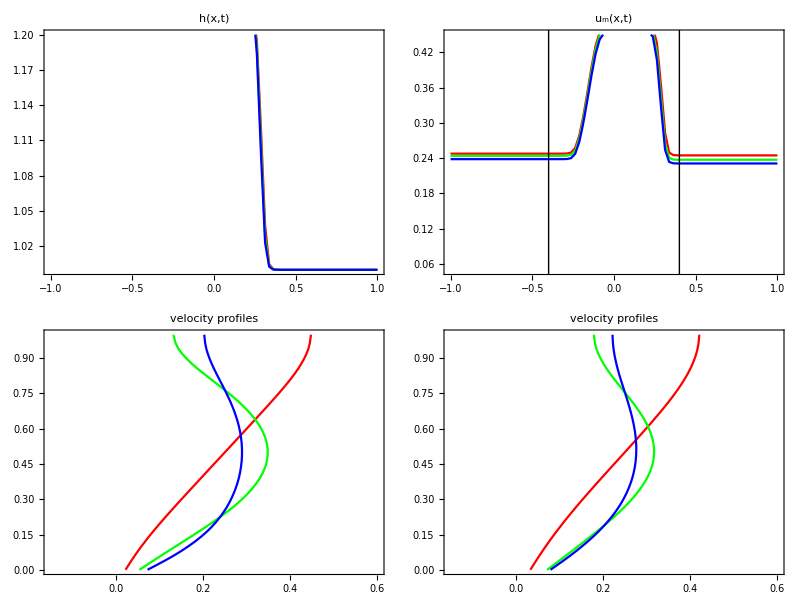

```mathematica
idx={1,2,3,4};

Grid[{{
Plot[Evaluate[Table[hLL[ix][x],{ix,idx}]],{x,x1,x2},
PlotRange->{{x1,x2},{1.0,1.2}},PlotStyle->color⟦1;;Length[idx]⟧,PlotLabel->"h(x,t)",
ImageSize->iSize,Frame->True],
Plot[Evaluate[Table[uMeanLL[ix][x],{ix,idx}]],{x,x1,x2},PlotRange->{{x1,x2},{0.05,0.45}},PlotStyle->color⟦1;;Length[idx]⟧,
PlotLabel->"u_m(x,t)",ImageSize->iSize,
Epilog->{Black,Thin,Line[{{0.4,-10},{0.4,10}}],Line[{{-0.4,-10},{-0.4,10}}]},Frame->True]
},{
ParametricPlot[Evaluate[Table[{uFullLL[ix][-0.4,y],y},{ix,idx}]],{y,y1,y2},AspectRatio->0.5,PlotRange->{{-0.15,0.6},{0,1}},PlotStyle->color⟦1;;Length[idx]⟧,
PlotLabel->"velocity profiles",Frame->True,ImageSize->iSize],
ParametricPlot[Evaluate[Table[{uFullLL[ix][0.4,y],y},{ix,idx}]],{y,y1,y2},AspectRatio->0.5,PlotRange->{{-0.15,0.6},{0,1}},PlotStyle->color⟦1;;Length[idx]⟧,
PlotLabel->"velocity profiles",Frame->True,ImageSize->iSize]
}},
Alignment->{{Right,Left},{Right,Left},{Right,Left}}
]
```